```mathematica
(*Parameters*)
γ=150; 
Dil=0.5; 
R0=0.5; 
ma=0.01; mb=0.1;mc=0.05; (*Example values for m parameters*)
TI=20;
δ = 0.5;

(*Define Imax and m as before*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Function for Req and Ce*)
ReqFunc[T_]:=m[T] R0/((1-δ) Imax[T]-m[T]);
CeFunc[T_, Req_, S_]:=Dil (S-Req)(Req + R0)/(Imax[T] Req);

(*Perform a simulation with independent draws for Req and T*)
numSimulations=10000; (*Number of simulations*)

simulationResults=Table[
Module[
{S,T, Ce},
(*Draw values for Req and T*)
S=RandomVariate[NormalDistribution[4,0.2]];
T=RandomVariate[NormalDistribution[20,2]];
(*Calculate Req and Ce based on S and T*)
Ce=CeFunc[T,ReqFunc[T],S];
{S,T, Ce}  (*Return the values*)],{numSimulations}];

(*Display the first few results*)
Take[simulationResults,10]
(*Calculate the 95th percentile*)
minValue=Min[simulationResults];
percentile95=Quantile[simulationResults[[All, 3]],0.95];
minValue
percentile95
```

General::munfl: Exp[-1277.62] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::munfl: Exp[-2553.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{3.86245,17.0815,Indeterminate},{4.0662,20.995,0.},{4.01822,17.9341,-2.66241×10^262},{4.13004,24.1257,Indeterminate},{4.23627,18.6564,0.},{4.26387,18.0608,0.},{3.9479,18.7205,0.},{3.65814,17.3287,Indeterminate},{4.04412,17.2484,Indeterminate},{3.8935,21.2435,0.}}

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Indeterminate,0.,-2.66241×10^262,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,9.52536,10.4561,«18»,0.,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.,0.,8.64321,9.16286,0.,0.,Indeterminate,-7.38848×10^33,ComplexInfinity,9.1346,«9950»},0.95].

Indeterminate

Quantile[{Indeterminate,0.,-2.66241×10^262,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,9.52536,10.4561,Indeterminate,-1.12437×10^226,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,9.07553,0.,0.,7.84955,0.,8.84874,0.,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.,0.,8.64321,9.16286,0.,0.,Indeterminate,-7.38848×10^33,ComplexInfinity,9.1346,ComplexInfinity,0.,Indeterminate,0.,0.,Indeterminate,9.41807,Indeterminate,0.,0.,0.,ComplexInfinity,9.02301,0.,9.46716,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,10.9794,9.55759,0.,Indeterminate,Indeterminate,7.94579,Indeterminate,ComplexInfinity,7.31931,0.,Indeterminate,Indeterminate,Indeterminate,8.96325,Indeterminate,0.,Indeterminate,8.38486,7.74308,0.,Indeterminate,Indeterminate,Indeterminate,10.1106,0.,0.,8.71691,-416.663,9.9309,-1.73758×10^227,7.17508,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,0.,0.,0.,7.61247,0.,8.87484,Indeterminate,8.45569,0.,9.19773,0.,9.53369,0.,0.,0.,8.91611,Indeterminate,0.,9.40065,0.,Indeterminate,0.,0.,Indeterminate,7.62184,0.,0.,0.,0.,0.,ComplexInfinity,0.,8.81317,0.,0.,Indeterminate,Indeterminate,0.,0.,8.96206,Indeterminate,0.,0.,Indeterminate,7.41719,9.4986,6.02902,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,ComplexInfinity,Indeterminate,0.,10.3818,Indeterminate,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,7.57613,0.,Indeterminate,0.,10.0019,-1.60805×10^114,Indeterminate,Indeterminate,-2.84675×10^181,Indeterminate,ComplexInfinity,0.,0.,0.,0.,0.,0.,-3.61076×10^10,0.,0.,0.,9.30544,Indeterminate,0.,0.,Indeterminate,0.,ComplexInfinity,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,9.31378,0.,Indeterminate,-5.16228×10^257,Indeterminate,9.1804,0.,9.4308,Indeterminate,0.,0.,0.,Indeterminate,ComplexInfinity,Indeterminate,9.29672,9.52286,0.,-1.2374×10^42,0.,0.,0.,9.30695,Indeterminate,-1.30645×10^177,0.,9.06641,-5.05075×10^190,0.,Indeterminate,0.,8.64417,Indeterminate,8.95597,-1.10266×10^61,0.,0.,9.24725,0.,Indeterminate,Indeterminate,8.76342,Indeterminate,0.,0.,Indeterminate,9.62412,0.,0.,7.9402,6.65054,0.,0.,Indeterminate,0.,0.,0.,Indeterminate,11.16,0.,0.,Indeterminate,9.71606,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,0.,8.68106,Indeterminate,8.39754,9.81327,0.,0.,0.,0.,0.,0.,-2.82913×10^152,0.,0.,7.64773,0.,0.,7.58024,0.,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,8.92249,Indeterminate,ComplexInfinity,10.0781,ComplexInfinity,8.58509,0.,8.26719,0.,8.95855,ComplexInfinity,Indeterminate,7.86267,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,ComplexInfinity,Indeterminate,0.,ComplexInfinity,Indeterminate,0.,9.47446,10.0382,Indeterminate,8.96239,0.,Indeterminate,Indeterminate,Indeterminate,9.32119,0.,-1.34766×10^103,Indeterminate,0.,0.,9.11149,Indeterminate,9.02595,0.,0.,0.,Indeterminate,0.,9.67165,ComplexInfinity,0.,0.,-1.91654×10^178,5.95018,0.,0.,Indeterminate,0.,0.,0.,0.,0.,8.69999,0.,-2.20519×10^286,0.,0.,0.,0.,0.,0.,0.,0.,8.93364,ComplexInfinity,5.28008,0.,9.51318,Indeterminate,Indeterminate,8.70338,0.,-8.4885×10^159,0.,9.03332,8.85659,0.,ComplexInfinity,-2.49129×10^30,0.,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,9.85076,0.,0.,Indeterminate,ComplexInfinity,Indeterminate,0.,Indeterminate,Indeterminate,8.94752,0.,0.,9.68944,9.61988,0.,0.,0.,8.65479,0.,0.,8.85655,Indeterminate,0.,0.,ComplexInfinity,Indeterminate,0.,8.7339,Indeterminate,0.,0.,0.,Indeterminate,0.,7.8858,Indeterminate,Indeterminate,0.,0.,-20.541,0.,0.,0.,0.,9.05148,0.,-5.08009×10^62,7.45069,0.,0.,Indeterminate,0.,8.64849,Indeterminate,0.,9.58569,Indeterminate,Indeterminate,9.43736,Indeterminate,0.,0.,0.,Indeterminate,-5.03662×10^26,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,Indeterminate,0.,0.,-3.23081×10^46,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,8.47484,0.,-6.417×10^30,7.80013,-3.27949×10^297,9.15269,9.64776,9.25687,9.5367,0.,Indeterminate,Indeterminate,-8.13346×10^138,0.,Indeterminate,0.,0.,0.,ComplexInfinity,-3.73223×10^40,Indeterminate,0.,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,0.,9.6703,Indeterminate,7.98597,0.,9.15413,Indeterminate,9.20388,Indeterminate,Indeterminate,0.,-1.20318×10^51,0.,Indeterminate,-4.00016×10^183,0.,-4.3254×10^239,0.,Indeterminate,0.,0.,-5.15055×10^152,0.,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,ComplexInfinity,Indeterminate,7.7358,0.,Indeterminate,8.26614,0.,0.,0.,7.62687,0.,0.,Indeterminate,6.95102,0.,9.34162,0.,Indeterminate,0.,0.,0.,8.81088,Indeterminate,0.,0.,0.,0.,0.,0.,0.,0.,0.,ComplexInfinity,9.06898,0.,0.,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,0.,9.39314,0.,9.14574,Indeterminate,-7.83601×10^19,0.,0.,9.33164,0.,-17.2126,0.,ComplexInfinity,0.,0.,8.62175,6.86798,ComplexInfinity,0.,ComplexInfinity,7.83206,Indeterminate,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,9.26411,Indeterminate,0.,0.,0.,0.,Indeterminate,9.22436,Indeterminate,Indeterminate,0.,0.,Indeterminate,-5.06993×10^68,-1.27422×10^151,12.2424,Indeterminate,9.22979,0.,0.,Indeterminate,Indeterminate,8.53149,6.78962,8.95551,Indeterminate,Indeterminate,0.,0.,6.39353,0.,0.,-2.617×10^61,0.,0.,0.,ComplexInfinity,0.,0.,9.16041,Indeterminate,11.9844,9.73564,Indeterminate,Indeterminate,0.,0.,Indeterminate,9.068,Indeterminate,Indeterminate,Indeterminate,8.28753,Indeterminate,8.69885,8.81302,Indeterminate,9.20276,Indeterminate,ComplexInfinity,0.,ComplexInfinity,9.75868,8.08623,Indeterminate,0.,0.,0.,10.6512,0.,0.,0.,8.07098,-8.4491×10^11,Indeterminate,Indeterminate,0.,0.,Indeterminate,-1.50492×10^87,0.,Indeterminate,0.,0.,7.7157,0.,Indeterminate,-5.24409×10^87,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,7.56951,0.,0.,0.,9.60821,0.,0.,Indeterminate,-6.23362×10^108,-2.85346×10^46,-172.506,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,ComplexInfinity,Indeterminate,0.,0.,-1.62152×10^207,0.,Indeterminate,0.,-3.14242×10^131,7.85086,-1.01692×10^42,-3.77158×10^56,Indeterminate,Indeterminate,10.1501,0.,0.,-1.16399×10^152,10.3794,0.,0.,-2.39222×10^173,7.48538,6.85759,0.,0.,0.,0.,Indeterminate,9.29189,0.,0.,7.71363,0.,0.,9.03908,0.,-2.01741×10^85,Indeterminate,Indeterminate,0.,Indeterminate,ComplexInfinity,0.,9.5354,0.,9.32523,0.,-9.20602×10^67,0.,0.,0.,0.,-18.5248,Indeterminate,0.,Indeterminate,0.,8.65198,0.,8.81634,8.58511,9.28789,0.,Indeterminate,7.28777,ComplexInfinity,0.,0.,0.,ComplexInfinity,0.,9.67428,Indeterminate,Indeterminate,0.,6.98954,0.,0.,Indeterminate,0.,0.,Indeterminate,8.20399,0.,9.17748,0.,7.90223,0.,9.71157,0.,Indeterminate,Indeterminate,0.,9.25934,0.,9.35692,Indeterminate,Indeterminate,ComplexInfinity,9.41277,ComplexInfinity,Indeterminate,0.,0.,0.,9.02679,0.,0.,10.1526,0.,ComplexInfinity,Indeterminate,9.24585,0.,8.89851,0.,9.46407,0.,0.,8.9404,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,8.54853,Indeterminate,9.27314,0.,0.,9.40376,0.,-5.62699×10^8,ComplexInfinity,0.,0.,Indeterminate,9.55745,0.,0.,Indeterminate,11.4573,8.61303,Indeterminate,0.,0.,0.,0.,ComplexInfinity,Indeterminate,-7.62456×10^107,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,-2.18054×10^57,6.90479,Indeterminate,ComplexInfinity,0.,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,-3.31598×10^134,0.,0.,-3.2271×10^111,9.26725,0.,0.,0.,-9.71852×10^100,0.,0.,Indeterminate,9.02517,8.91644,Indeterminate,ComplexInfinity,ComplexInfinity,-5.41949×10^179,0.,9.0507,0.,0.,0.,9.5824,0.,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,9.18668,ComplexInfinity,0.,-3.20935×10^95,0.,0.,0.,9.82297,8.71435,Indeterminate,9.20924,0.,0.,0.,0.,0.,9.43662,9.14331,0.,0.,0.,0.,8.65364,ComplexInfinity,9.12116,0.,0.,0.,Indeterminate,Indeterminate,0.,9.01833,Indeterminate,ComplexInfinity,0.,-28.8658,0.,9.62157,0.,9.03597,Indeterminate,0.,Indeterminate,0.,0.,8.32809,0.,Indeterminate,0.,7.33152,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,9.21865,Indeterminate,0.,8.80057,0.,0.,Indeterminate,Indeterminate,0.,-421.171,0.,9.53215,0.,Indeterminate,-287.267,0.,16.6009,9.76296,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,0.,8.69257,Indeterminate,8.93573,0.,8.33632,Indeterminate,0.,9.49412,-4.51789×10^79,10.0392,8.52479,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,0.,ComplexInfinity,0.,0.,0.,0.,0.,Indeterminate,129.495,0.,0.,0.,Indeterminate,0.,0.,9.35344,0.,Indeterminate,0.,0.,ComplexInfinity,0.,0.,0.,0.,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,9.46099,0.,0.,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,ComplexInfinity,9.8711,Indeterminate,0.,8.70071,0.,0.,9.21537,10.201,0.,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,ComplexInfinity,7.9485,8.48113,0.,0.,0.,Indeterminate,Indeterminate,7.8474,0.,0.,Indeterminate,Indeterminate,Indeterminate,9.61959,-2.95405×10^67,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,0.,0.,9.2392,Indeterminate,9.95031,0.,Indeterminate,Indeterminate,Indeterminate,0.,8.86691,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,9.44386,0.,0.,0.,0.,0.,0.,-3.12979×10^145,0.,0.,Indeterminate,8.9128,0.,9.37149,0.,-2.77859×10^181,Indeterminate,0.,-3.60963×10^96,0.,-2.19984×10^167,Indeterminate,0.,Indeterminate,9.41598,Indeterminate,Indeterminate,9.50012,0.,0.,0.,Indeterminate,0.,0.,0.,0.,-7.68083×10^52,10.444,10.9403,0.,0.,8.97556,9.04334,0.,-1.37612×10^88,0.,Indeterminate,0.,9.16636,Indeterminate,Indeterminate,-1.61308×10^11,Indeterminate,ComplexInfinity,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,0.,0.,Indeterminate,-7.66493×10^80,0.,Indeterminate,0.,0.,0.,0.,8.99468,0.,0.,0.,Indeterminate,Indeterminate,0.,-2.32513×10^42,Indeterminate,Indeterminate,0.,0.,8.41195,Indeterminate,0.,0.,9.27566,9.2122,0.,0.,0.,6.90972,0.,5.66914,-1.41669×10^205,0.,Indeterminate,-3.34984×10^53,Indeterminate,0.,10.0878,Indeterminate,0.,0.,0.,-3.93581×10^96,Indeterminate,0.,Indeterminate,Indeterminate,0.,5.24152,0.,-64106.9,0.,9.04868,0.,0.,0.,Indeterminate,0.,ComplexInfinity,0.,8.87835,7.98649,0.,0.,0.,6.51969,0.,8.58184,Indeterminate,8.73517,-5.96836×10^159,-1.08048×10^224,9.08744,-1.98221×10^80,Indeterminate,0.,0.,0.,0.,9.70008,0.,Indeterminate,0.,-3.92739×10^17,0.,0.,Indeterminate,0.,0.,10.3764,-3.37212×10^69,8.75151,0.,-1.40414×10^143,Indeterminate,9.13645,Indeterminate,8.75522,9.54762,0.,Indeterminate,0.,ComplexInfinity,0.,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,2.52544,Indeterminate,Indeterminate,0.,8.69488,8.87679,11.1839,-7.90083×10^118,7.45904,ComplexInfinity,-1.58145×10^208,0.,9.50378,-2.55602×10^50,0.,0.,6.71835,6.21451,8.47987,0.,Indeterminate,Indeterminate,8.74816,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,ComplexInfinity,9.13518,0.,0.,9.56132,8.10583,Indeterminate,9.39366,Indeterminate,0.,9.18845,20.4444,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,-1.33709×10^200,Indeterminate,ComplexInfinity,0.,Indeterminate,9.16723,0.,Indeterminate,0.,9.72595,0.,0.,8.91217,0.,Indeterminate,0.,ComplexInfinity,8.33149,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,0.,9.17656,-6.47057×10^20,Indeterminate,0.,0.,-3.19394×10^19,Indeterminate,0.,0.,ComplexInfinity,0.,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,0.,7.65148,0.,7.59207,-5.4351×10^76,6.46326,0.,Indeterminate,0.,-1.77333×10^54,10.296,0.,0.,0.,0.,0.,Indeterminate,-8.85401×10^241,Indeterminate,0.,9.40693,0.,0.,ComplexInfinity,9.48308,0.,8.66213,0.,Indeterminate,ComplexInfinity,8.42789,0.,8.85991,9.24886,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,8.48073,0.,ComplexInfinity,Indeterminate,0.,Indeterminate,Indeterminate,0.,11.3881,0.,12.1679,-1.75315×10^77,9.12233,0.,0.,0.,0.,0.,0.,-9.09374×10^21,0.,Indeterminate,0.,0.,9.52541,0.,0.,0.,0.,0.,Indeterminate,8.42603,8.06514,0.,0.,0.,9.34647,-8.40744×10^124,0.,5.01404,7.61499,9.86835,Indeterminate,0.,0.,Indeterminate,-1.74135×10^186,Indeterminate,7.78872,Indeterminate,0.,-3.91557×10^94,Indeterminate,8.79195,8.38358,0.,7.47729,Indeterminate,9.71907,9.07079,Indeterminate,0.,0.,Indeterminate,ComplexInfinity,0.,8.68753,8.8837,0.,0.,0.,0.,7.76391,0.,0.,0.,9.42882,0.,0.,0.,0.,ComplexInfinity,0.,0.,0.,7.56176,0.,0.,0.,8.61643,Indeterminate,0.,Indeterminate,0.,9.47923,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,9.19082,0.,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,9.12004,ComplexInfinity,8.81322,9.50376,0.,9.2238,Indeterminate,Indeterminate,ComplexInfinity,ComplexInfinity,0.,0.,Indeterminate,0.,7.16303,0.,Indeterminate,0.,0.,ComplexInfinity,-3.99304×10^128,9.19902,7.59531,0.,0.,0.,-4.54146×10^25,8.05124,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,-1.19227×10^93,0.,0.,0.,Indeterminate,-1.83343×10^73,0.,9.14044,0.,ComplexInfinity,0.,8.92338,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,8.26682,0.,-8.62766×10^220,ComplexInfinity,-1.57378×10^77,-1.01846×10^110,8.9487,0.,Indeterminate,ComplexInfinity,9.20265,9.14945,-1.52113×10^184,8.82822,0.,0.,0.,0.,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,Indeterminate,Indeterminate,-4.50399×10^38,Indeterminate,7.4353,0.,0.,8.72407,0.,Indeterminate,0.,8.94176,Indeterminate,0.,Indeterminate,Indeterminate,-1.24084×10^24,Indeterminate,8.36305,-4.79696×10^7,9.68468,0.,Indeterminate,0.,-4.01656×10^231,Indeterminate,0.,Indeterminate,7.03626,0.,0.,Indeterminate,-1.50243×10^33,0.,7.70223,Indeterminate,0.,0.,0.,0.,0.,0.,8.85207,0.,Indeterminate,9.28439,Indeterminate,Indeterminate,-8.03269×10^12,Indeterminate,0.,9.92704,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,0.,9.03688,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,0.,0.,0.,0.,-5.70695×10^6,-7.44616×10^52,-9.17736×10^45,0.,Indeterminate,10.7881,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,7.64288,Indeterminate,9.344,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,-9.93702×10^199,Indeterminate,-1.14963×10^240,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,0.,-3.56812×10^61,8.83065,Indeterminate,8.5979,0.,-2.95038×10^275,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,-1.4298×10^30,8.67868,0.,-2833.58,0.,0.,0.,0.,11.5378,6.88376,0.,Indeterminate,0.,0.,0.,-4.63014×10^144,0.,0.,9.05066,Indeterminate,0.,8.89263,Indeterminate,0.,0.,-2.83538×10^269,-6.29307×10^160,ComplexInfinity,Indeterminate,0.,0.,0.,0.,0.,8.02567,-4.80345×10^139,0.,-4.63422×10^109,Indeterminate,Indeterminate,0.,8.78459,Indeterminate,Indeterminate,9.34092,-5.39639×10^222,0.,Indeterminate,ComplexInfinity,ComplexInfinity,0.,0.,0.,0.,Indeterminate,9.04,0.,0.,0.,0.,-2.65737×10^20,0.,9.49718,Indeterminate,Indeterminate,8.58753,Indeterminate,0.,9.67973,Indeterminate,Indeterminate,-3.42236×10^19,0.,0.,ComplexInfinity,0.,0.,-2.9913×10^76,0.,Indeterminate,Indeterminate,9.63244,8.66395,0.,9.1074,0.,Indeterminate,Indeterminate,0.,8.62754,0.,-1.71152×10^43,0.,0.,ComplexInfinity,0.,Indeterminate,0.,0.,8.88353,Indeterminate,0.,0.,ComplexInfinity,0.,0.,0.,Indeterminate,9.83029,0.,8.25762,Indeterminate,0.,-5.33835×10^157,Indeterminate,8.78348,0.,9.52297,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,-4.95561×10^294,Indeterminate,8.60003,0.,8.80231,0.,0.,0.,0.,10.7417,9.32803,Indeterminate,ComplexInfinity,0.,0.,0.,0.,8.76591,9.37362,0.,0.,8.83241,Indeterminate,0.,8.77271,Indeterminate,0.,0.,Indeterminate,0.,ComplexInfinity,7.85762,Indeterminate,Indeterminate,8.73791,0.,2.98672,7.46305,Indeterminate,0.,Indeterminate,0.,Indeterminate,10.1902,0.,0.,0.,Indeterminate,0.,8.49034,0.,9.13219,9.08077,8.82589,0.,9.74263,-1.6603×10^51,0.,0.,Indeterminate,0.,-7.87241×10^278,Indeterminate,Indeterminate,-281097.,0.,Indeterminate,8.9614,Indeterminate,0.,6.85892,9.11122,Indeterminate,0.,Indeterminate,ComplexInfinity,-5.22297×10^244,9.62492,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,8.04231,Indeterminate,Indeterminate,0.,ComplexInfinity,0.,11.1366,0.,9.5087,0.,-2.15805×10^118,ComplexInfinity,0.,0.,9.00668,0.,0.,8.63323,0.,0.,0.,0.,0.,7.66058,-2.31851×10^265,9.74551,0.,8.70277,Indeterminate,0.,0.,Indeterminate,0.,9.13831,8.73657,0.,0.,8.81282,-7.00528×10^62,7.75704,0.,0.,ComplexInfinity,0.,0.,0.,Indeterminate,8.6661,9.654,0.,0.,-4.75949×10^13,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,-8.15954×10^32,0.,12.6671,8.76348,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,8.75928,5.81147,Indeterminate,Indeterminate,9.77653,0.,0.,Indeterminate,0.,0.,ComplexInfinity,Indeterminate,10.0271,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,0.,8.56842,0.,0.,ComplexInfinity,0.,-1.7798×10^102,Indeterminate,9.12809,Indeterminate,9.58761,0.,0.,0.,0.,0.,Indeterminate,8.58379,0.,Indeterminate,ComplexInfinity,5.74292,0.,8.78126,0.,0.,Indeterminate,10.0416,9.63436,ComplexInfinity,0.,0.,-3.20751×10^20,Indeterminate,Indeterminate,-6.408×10^194,Indeterminate,0.,0.,0.,ComplexInfinity,ComplexInfinity,8.67046,0.,0.,Indeterminate,7.7727,0.,0.,Indeterminate,25.1948,0.,0.,Indeterminate,-18.5278,0.,8.96536,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,0.,0.,0.,7.60592,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,0.,0.,0.,7.46614,8.64854,0.,8.00185,0.,Indeterminate,0.,7.87372,0.,Indeterminate,9.17758,0.,0.,ComplexInfinity,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,-7.50845×10^26,0.,0.,9.09372,Indeterminate,8.75213,0.,10.5637,0.,-8688.67,9.14985,0.,Indeterminate,0.,Indeterminate,6.90848,0.,9.25854,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,0.,0.,7.95933,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,8.55728,0.,0.,9.00824,Indeterminate,0.,9.13514,0.,0.,0.,0.,0.,0.,Indeterminate,0.,ComplexInfinity,8.96626,0.,6.47836,0.,0.,0.,0.,Indeterminate,ComplexInfinity,0.,9.52479,-1.39393×10^82,Indeterminate,0.,0.,ComplexInfinity,0.,0.,8.63006,Indeterminate,9.28471,-1.89515×10^12,7.91948,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,9.22339,ComplexInfinity,0.,8.97275,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,8.81918,0.,0.,Indeterminate,0.,9.14664,ComplexInfinity,0.,8.38497,0.,0.,9.10404,0.,8.85046,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,-1.76055×10^6,0.,ComplexInfinity,0.,0.,0.,-1.35553×10^53,0.,Indeterminate,0.,7.87312,0.,-1.39323×10^131,0.,8.96041,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,9.29048,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,0.,10.0467,9.77354,-4.11299×10^6,7.30237,0.,Indeterminate,0.,15.4207,8.73939,Indeterminate,9.166,8.57738,0.,0.,0.,0.,0.,0.,0.,0.,15.0697,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,-1.76934×10^76,-8.06139×10^125,0.,0.,Indeterminate,0.,0.,8.98474,0.,0.,8.53369,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,9.53869,0.,0.,7.7802,0.,Indeterminate,9.17312,0.,0.,11.4013,-1.01865×10^153,0.,Indeterminate,Indeterminate,9.6924,0.,8.58946,0.,8.03054,Indeterminate,0.,0.,0.,0.,0.,9.51428,0.,0.,0.,Indeterminate,0.,0.,0.,0.,0.,7.83535,0.,0.,Indeterminate,0.,0.,0.,9.67952,0.,Indeterminate,0.,9.71635,0.,0.,0.,Indeterminate,8.05487,-9.39549×10^267,Indeterminate,0.,9.03478,8.03068,Indeterminate,0.,0.,8.66565,0.,9.65945,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,8.8701,0.,Indeterminate,-9.09551×10^92,0.,Indeterminate,0.,0.,0.,0.,9.66576,0.,0.,7.01893,6.59321,0.,0.,ComplexInfinity,0.,0.,ComplexInfinity,8.93785,0.,7.52249,0.,8.85525,Indeterminate,ComplexInfinity,19.9574,0.,0.,8.68608,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,0.,0.,0.,0.,-3.3899×10^36,Indeterminate,0.,-2.16325×10^125,0.,0.,0.,-3.32659×10^19,Indeterminate,-70788.6,0.,0.,Indeterminate,Indeterminate,Indeterminate,9.21796,Indeterminate,0.,0.,0.,-1.21081×10^199,9.16833,0.,0.,0.,ComplexInfinity,Indeterminate,Indeterminate,11.0002,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,ComplexInfinity,10.0224,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,ComplexInfinity,0.,9.26191,0.,9.56289,Indeterminate,Indeterminate,0.,Indeterminate,-7.96557×10^14,0.,Indeterminate,Indeterminate,8.99149,0.,0.,ComplexInfinity,0.,9.48457,0.,-5.72082×10^74,0.,0.,0.,0.,8.83302,0.,-5.57717×10^149,Indeterminate,0.,9.05616,8.86496,0.,ComplexInfinity,0.,0.,Indeterminate,0.,-2.49167×10^101,0.,Indeterminate,0.,0.,0.,0.,0.,-1.68421×10^180,Indeterminate,0.,0.,0.,Indeterminate,9.15207,0.,8.99915,0.,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,8.91545,0.,Indeterminate,0.,Indeterminate,-7.31973×10^67,Indeterminate,Indeterminate,0.,0.,8.65257,Indeterminate,0.,0.,9.55494,0.,0.,7.51616,0.,0.,0.,Indeterminate,0.,8.60363,0.,8.62674,-1.2618×10^169,0.,0.,0.,0.,-2.51672×10^81,Indeterminate,-5.15058×10^39,-5.17628×10^131,-6.57795×10^104,ComplexInfinity,Indeterminate,Indeterminate,0.,20.9121,0.,Indeterminate,Indeterminate,-3.07705×10^155,Indeterminate,9.38133,0.,0.,Indeterminate,0.,9.23899,0.,0.,7.8433,0.,0.,0.,0.,0.,Indeterminate,9.16031,0.,0.,0.,Indeterminate,0.,0.,0.,0.,0.,0.,-9.40015×10^127,Indeterminate,0.,0.,0.,-1.49196×10^30,0.,10.47,0.,Indeterminate,0.,0.,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,9.51978,0.,9.68802,0.,0.,-1.19867×10^138,0.,0.,9.1724,0.,9.34527,Indeterminate,-1.653×10^155,-9.05705×10^148,0.,0.,ComplexInfinity,ComplexInfinity,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,9.26226,Indeterminate,8.38687,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,-3.85695×10^191,Indeterminate,0.,Indeterminate,Indeterminate,0.,8.0667,Indeterminate,-4.85265×10^171,0.,0.,0.,0.,ComplexInfinity,0.,9.53948,0.,0.,0.,12.6555,8.66313,0.,ComplexInfinity,0.,10.165,9.13862,0.,0.,0.,0.,Indeterminate,0.,0.,9.07764,0.,0.,0.,9.57178,0.,-5.08122×10^38,0.,Indeterminate,0.,-4.9952×10^48,0.,0.,0.,8.93755,0.,0.,0.,8.80358,0.,7.77628,-2.19594×10^71,0.,0.,Indeterminate,Indeterminate,ComplexInfinity,7.24871,Indeterminate,-1.39088×10^87,Indeterminate,9.04667,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,6.97906,10.1129,Indeterminate,Indeterminate,Indeterminate,0.,9.43479,Indeterminate,9.83739,Indeterminate,0.,0.,8.86347,9.79394,0.,0.,0.,-9.87671×10^77,0.,Indeterminate,-14610.3,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,6.99957,0.,0.,Indeterminate,Indeterminate,9.60229,-1.42561×10^200,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,-4.92266×10^292,0.,Indeterminate,8.66655,0.,0.,0.,6.98441,Indeterminate,Indeterminate,8.551,0.,-3.97283×10^283,0.,7.59597,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,8.45144,Indeterminate,Indeterminate,0.,0.,9.3446,ComplexInfinity,8.74618,Indeterminate,Indeterminate,0.,7.56117,0.,0.,Indeterminate,7.51469,0.,8.44291,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-1.19553×10^159,-4.76616×10^296,0.,Indeterminate,Indeterminate,0.,0.,-2.67543×10^151,Indeterminate,7.25757,0.,0.,9.24972,Indeterminate,Indeterminate,0.,9.18363,0.,Indeterminate,0.,Indeterminate,0.,ComplexInfinity,0.,Indeterminate,0.,9.19114,0.,0.,Indeterminate,9.34088,0.,5.6612,0.,-3.20398×10^20,Indeterminate,9.23664,Indeterminate,Indeterminate,0.,Indeterminate,9.62423,Indeterminate,0.,0.,ComplexInfinity,0.,0.,ComplexInfinity,Indeterminate,0.,0.,8.61233,Indeterminate,0.,Indeterminate,9.85575,9.27616,Indeterminate,0.,9.24096,0.,0.,0.,0.,0.,8.94104,Indeterminate,0.,0.,0.,-4.86477×10^122,Indeterminate,Indeterminate,9.05616,8.99575,Indeterminate,Indeterminate,9.32048,8.44934,0.,8.73956,Indeterminate,29.8618,-5.12583×10^186,0.,0.,ComplexInfinity,0.,Indeterminate,0.,Indeterminate,7.63657,-1.03418×10^296,-7.17642×10^32,0.,ComplexInfinity,7.68281,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,-43.4262,0.,9.00807,0.,0.,0.,ComplexInfinity,Indeterminate,-2.84432×10^62,Indeterminate,0.,0.,9.4861,0.,Indeterminate,0.,9.04321,0.,0.,Indeterminate,Indeterminate,0.,0.,7.3584,9.55486,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,-1.21418×10^140,Indeterminate,7.77354,Indeterminate,0.,8.73652,0.,10.8408,0.,0.,0.,-3.33787×10^87,0.,0.,0.,0.,Indeterminate,0.,0.,9.16107,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,9.00705,0.,9.05585,Indeterminate,-3.17753×10^76,0.,0.,8.96935,9.05292,9.00216,9.50033,ComplexInfinity,7.82682,Indeterminate,7.67994,0.,Indeterminate,7.41645,0.,0.,0.,Indeterminate,0.,ComplexInfinity,7.95779,-8.35644×10^132,0.,8.29072,0.,8.86607,8.75147,Indeterminate,0.,Indeterminate,9.214,Indeterminate,7.06574,0.,0.,0.,0.,8.79221,8.56724,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,0.,9.12832,0.,0.,7.55467,Indeterminate,0.,0.,0.,9.67525,0.,0.,Indeterminate,9.07846,0.,9.49695,0.,0.,0.,-1.04544×10^211,0.,0.,Indeterminate,0.,0.,0.,0.,0.,-6.98938×10^98,0.,Indeterminate,Indeterminate,0.,0.,2.45174,0.,9.95707,9.44447,8.54144,Indeterminate,0.,31.7116,0.,Indeterminate,0.,0.,-9.17027×10^92,0.,0.,Indeterminate,ComplexInfinity,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,9.28528,0.,8.30898,0.,0.,0.,0.,Indeterminate,0.,8.97513,0.,Indeterminate,9.23294,8.94597,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,6.5899,0.,Indeterminate,ComplexInfinity,10.2917,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,8.86569,9.17027,0.,0.,0.,8.27935,0.,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,13.4747,0.,9.2797,0.,8.10943,Indeterminate,8.82995,0.,0.,8.8377,0.,0.,0.,Indeterminate,Indeterminate,0.,8.80447,0.,0.,0.,0.,Indeterminate,0.,0.,5.49045,ComplexInfinity,0.,0.,10.0179,Indeterminate,0.,0.,0.,9.15134,Indeterminate,8.8491,6.85258,-5.44028×10^16,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,-1.75629×10^94,0.,0.,8.41704,Indeterminate,0.,0.,Indeterminate,0.,9.36419,10.7664,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.04418,0.,0.,0.,0.,-3.50366×10^201,9.36664,ComplexInfinity,0.,7.65927,0.,0.,0.,-4.79646×10^259,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,7.03123,0.,0.,0.,-2.72523×10^69,8.76654,-12.0111,-1.55623×10^214,9.36352,0.,0.,-2.30875×10^138,0.,9.40779,0.,9.42412,Indeterminate,0.,Indeterminate,0.,0.,8.62366,Indeterminate,0.,0.,0.,-7.82431×10^14,9.00765,Indeterminate,9.54388,0.,0.,Indeterminate,0.,0.,8.67164,0.,0.,Indeterminate,Indeterminate,9.41364,9.51518,0.,0.,0.,ComplexInfinity,0.,0.,0.,Indeterminate,0.,Indeterminate,8.62037,9.35106,0.,0.,0.,0.,8.84503,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,-2.35541×10^280,9.27987,0.,0.,Indeterminate,0.,Indeterminate,9.08159,Indeterminate,0.,0.,9.64793,0.,0.,0.,0.,ComplexInfinity,Indeterminate,-7.42913×10^87,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,Indeterminate,ComplexInfinity,-2.69436×10^187,10.6316,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,8.57503,-1.68525×10^59,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,9.71538,0.,Indeterminate,Indeterminate,0.,Indeterminate,9.81078,6.7153,-1.02855×10^22,Indeterminate,0.,Indeterminate,11.6534,9.45773,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,8.8756,-2.82627×10^34,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,8.90799,10.551,-1.53056×10^118,-3.64275×10^289,-1.30407×10^38,Indeterminate,0.,0.,0.,12.038,0.,0.,-7.28915×10^23,0.,0.,0.,-2.78867×10^58,0.,-1.37282×10^57,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,0.,-1.06168×10^276,9.03433,8.43131,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,8.6623,0.,0.,-3.56506×10^24,0.,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,8.34833,0.,0.,0.,8.94955,0.,Indeterminate,Indeterminate,0.,Indeterminate,-6.64023×10^8,0.,0.,9.88555,0.,-3.53503×10^175,-3.38962×10^113,ComplexInfinity,9.04227,8.51057,8.81307,6.07449,-6.34697,-1.93725×10^21,0.,Indeterminate,0.,-1.49978×10^38,0.,0.,8.81079,7.72721,8.50899,ComplexInfinity,0.,-2.87907×10^263,Indeterminate,0.,Indeterminate,0.,-1.45948×10^183,Indeterminate,-1.79722×10^86,0.,10.0143,0.,8.76207,0.,0.,10.0217,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,6.56305,ComplexInfinity,8.31559,8.88741,Indeterminate,-2.4447×10^211,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,0.,9.54844,0.,0.,0.,0.,Indeterminate,9.56629,0.,7.33012,-1.37597×10^193,8.944,0.,0.,-1.4806×10^9,0.,10.9631,0.,ComplexInfinity,Indeterminate,Indeterminate,ComplexInfinity,Indeterminate,0.,8.62968,0.,0.,Indeterminate,0.,9.34676,0.,Indeterminate,8.76252,0.,-1.01447×10^18,-4.09546×10^138,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,-5.54455×10^270,0.,0.,9.71826,Indeterminate,Indeterminate,0.,ComplexInfinity,0.,8.95999,0.,0.,0.,Indeterminate,0.,-4.16823×10^131,0.,7.57288,-3.1564×10^22,Indeterminate,0.,0.,0.,9.07671,-8.67477×10^248,9.26424,Indeterminate,Indeterminate,ComplexInfinity,ComplexInfinity,0.,ComplexInfinity,-5.26338×10^17,ComplexInfinity,9.05074,0.,9.10843,6.78444,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,ComplexInfinity,ComplexInfinity,-7.5554×10^187,0.,Indeterminate,0.,0.,9.49336,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,9.50634,ComplexInfinity,Indeterminate,0.,7.58548,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,10.2478,0.,0.,Indeterminate,0.,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,8.54803,9.8599,9.27783,Indeterminate,0.,9.18692,ComplexInfinity,7.60151,0.,Indeterminate,0.,0.,0.,Indeterminate,8.12469,9.03048,Indeterminate,9.25984,0.,7.72387,8.25398,0.,Indeterminate,0.,0.,9.11945,8.82727,Indeterminate,0.,0.,0.,Indeterminate,-3.35598×10^111,ComplexInfinity,7.93067,0.,Indeterminate,6.31797,8.07202,ComplexInfinity,0.,Indeterminate,0.,7.57479,Indeterminate,0.,0.,0.,0.,0.,0.,8.84772,ComplexInfinity,0.,0.,0.,9.14899,0.,0.,Indeterminate,8.88392,0.,9.31936,Indeterminate,10.0806,0.,-4.48985×10^68,0.,0.,8.09813,9.08498,Indeterminate,5.89549,0.,0.,0.,0.,-7.24077×10^8,ComplexInfinity,8.72881,0.,0.,0.,Indeterminate,-2.36256×10^64,ComplexInfinity,0.,0.,8.60045,9.30201,-2.40746×10^145,0.,ComplexInfinity,10.5426,0.,Indeterminate,Indeterminate,7.0008,0.,0.,0.,0.,0.,0.,Indeterminate,10.4988,7.00079,9.26651,0.,0.,0.,0.,Indeterminate,0.,0.,9.73316,0.,9.28047,Indeterminate,0.,-2.01757×10^22,Indeterminate,ComplexInfinity,0.,0.,10.3962,0.,0.,8.84903,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,ComplexInfinity,0.,ComplexInfinity,0.,-1.2058×10^26,Indeterminate,0.,7.46064,0.,0.,0.,-6.27773×10^32,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,-7.68277×10^243,9.26257,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,0.,-3.82507×10^121,0.,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,7.28949,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,8.27595,0.,Indeterminate,0.,9.41381,0.,9.69749,0.,0.,Indeterminate,0.,8.85021,0.,Indeterminate,0.,0.,Indeterminate,8.81675,9.35857,-18.4379,8.55568,10.1597,Indeterminate,Indeterminate,7.18016,0.,0.,ComplexInfinity,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,9.84751,0.,0.,0.,Indeterminate,Indeterminate,-1.40888×10^10,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,9.4127,0.,Indeterminate,Indeterminate,-5.68156×10^93,Indeterminate,Indeterminate,0.,-8.2088×10^121,0.,0.,0.,0.,-8.3079×10^79,0.,ComplexInfinity,-1.08381×10^36,9.39237,0.,8.90658,ComplexInfinity,0.,Indeterminate,9.10427,Indeterminate,0.,0.,0.,8.48785,0.,-1.46098×10^37,0.,0.,Indeterminate,9.38592,Indeterminate,8.81332,0.,0.,0.,9.26616,0.,0.,7.70953,-12177.4,0.,0.,0.,0.,0.,7.52548,7.82246,0.,9.74234,Indeterminate,10.041,0.,0.,0.,ComplexInfinity,Indeterminate,9.54056,-7.95432×10^113,0.,0.,7.68726,Indeterminate,0.,0.,-9.08294×10^33,0.,10.0484,9.11437,-4.46367×10^70,0.,0.,0.,8.27376,0.,0.,Indeterminate,ComplexInfinity,Indeterminate,0.,14.6046,0.,0.,17.2138,Indeterminate,0.,Indeterminate,-1.22517×10^60,0.,0.,-7.87889×10^283,7.58996,Indeterminate,Indeterminate,0.,ComplexInfinity,9.9701,Indeterminate,0.,-5.24243×10^104,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,ComplexInfinity,0.,-1.19375×10^203,0.,0.,9.45308,0.,0.,0.,0.,Indeterminate,9.66562,9.15161,0.,Indeterminate,0.,9.46523,0.,0.,0.,0.,Indeterminate,0.,9.07702,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,9.13369,-6.98798×10^8,0.,-8.04323×10^71,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,0.,9.09029,0.,0.,Indeterminate,-2.62486×10^124,0.,0.,Indeterminate,0.,9.36045,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,9.2959,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,9.24654,-4.79412×10^61,0.,0.,Indeterminate,0.,0.,0.,0.,-6.86613×10^180,0.,9.12345,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,9.13319,Indeterminate,-8.24275×10^214,Indeterminate,Indeterminate,8.25914,0.,0.,8.95283,10.3481,0.,10.0764,9.84429,Indeterminate,-6.75674×10^37,Indeterminate,0.,9.18425,8.94621,0.,9.17311,0.,0.,0.,9.56394,Indeterminate,Indeterminate,7.57568,ComplexInfinity,0.,6.82094,Indeterminate,0.,Indeterminate,8.28539,0.,0.,0.,0.,0.,0.,Indeterminate,0.,9.50273,7.50375,9.08487,0.,0.,0.,-1.11094×10^86,6.73051,9.18839,0.,-3.36367×10^208,0.,0.,-2.18336×10^12,Indeterminate,0.,0.,8.70442,0.,Indeterminate,0.,0.,9.93398,0.,ComplexInfinity,ComplexInfinity,0.,0.,0.,9.37562,9.15422,0.,-5.26854×10^17,Indeterminate,9.30216,9.0748,0.,8.94441,0.,9.26233,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,7.47719,0.,9.13414,Indeterminate,9.17799,9.60064,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,ComplexInfinity,-4.5727×10^32,0.,0.,Indeterminate,0.,ComplexInfinity,0.,10.8458,Indeterminate,0.,0.,7.29,0.,8.83061,Indeterminate,0.,0.,8.5583,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,0.,0.,8.21673,0.,8.3679,Indeterminate,Indeterminate,0.,Indeterminate,8.30936,8.63606,0.,0.,0.,0.,-1.10168×10^153,Indeterminate,9.17293,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,8.62788,Indeterminate,13.889,0.,9.86633,0.,0.,0.,0.,-2.17074×10^142,8.40595,Indeterminate,-2.77392×10^13,0.,Indeterminate,8.97809,0.,0.,0.,0.,0.,0.,8.66713,9.12025,Indeterminate,0.,8.04585,0.,0.,0.,8.80065,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,ComplexInfinity,Indeterminate,0.,0.,-2.68808×10^207,8.69053,Indeterminate,8.83001,0.,-2.84463×10^262,0.,9.47828,7.52987,0.,0.,Indeterminate,Indeterminate,9.06436,Indeterminate,ComplexInfinity,0.,8.06713,0.,0.,Indeterminate,0.,Indeterminate,8.50695,Indeterminate,0.,8.86179,Indeterminate,0.,8.45916,Indeterminate,Indeterminate,0.,7.01401,Indeterminate,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,10.0173,0.,0.,9.8693,Indeterminate,8.48845,Indeterminate,0.,0.,0.,0.,0.,0.,Indeterminate,8.93195,0.,-4.60468×10^153,0.,9.80672,0.,-2.29958×10^58,0.,8.53167,Indeterminate,8.88792,ComplexInfinity,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,9.24986,0.,0.,Indeterminate,0.,0.,9.52725,0.,Indeterminate,0.,Indeterminate,Indeterminate,8.96447,Indeterminate,0.,-1.2608×10^32,0.,ComplexInfinity,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,8.23771,0.,9.27908,ComplexInfinity,0.,0.,0.,-1.32415×10^14,0.,Indeterminate,0.,ComplexInfinity,8.50086,0.,-1.13495×10^10,Indeterminate,5.89035,Indeterminate,0.,Indeterminate,Indeterminate,-1.62514×10^236,Indeterminate,0.,8.909,0.,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,8.17665,0.,Indeterminate,0.,ComplexInfinity,Indeterminate,0.,0.,-3.8897×10^200,0.,Indeterminate,7.4445,10.3475,Indeterminate,8.7615,8.84251,0.,Indeterminate,-1.1338×10^115,0.,-9.21227×10^59,0.,0.,0.,0.,-8.87473×10^24,0.,Indeterminate,0.,9.38242,4.30845,0.,9.31028,9.36113,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,9.46636,9.53582,0.,0.,Indeterminate,8.75724,0.,ComplexInfinity,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,8.49782,0.,Indeterminate,0.,Indeterminate,9.41614,0.,Indeterminate,-7.21611×10^23,0.,0.,Indeterminate,0.,0.,0.,8.51291,0.,0.,0.,0.,0.,0.,Indeterminate,0.,9.85705,0.,Indeterminate,8.58809,0.,-9.00251×10^28,38.9248,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,9.61985,0.,Indeterminate,9.11538,ComplexInfinity,-1.94803×10^24,0.,-1.18964×10^86,-2.30861×10^55,8.2343,7.36208,0.,Indeterminate,0.,2.54774,Indeterminate,Indeterminate,0.,0.,0.,7.40496,Indeterminate,0.,0.,0.,ComplexInfinity,Indeterminate,0.,Indeterminate,ComplexInfinity,6.90974,8.97502,8.76376,0.,Indeterminate,ComplexInfinity,0.,ComplexInfinity,Indeterminate,0.,Indeterminate,Indeterminate,9.08616,0.,-3.03188×10^84,8.91457,Indeterminate,0.,0.,0.,8.31762,8.54286,0.,Indeterminate,Indeterminate,-3.82602×10^49,Indeterminate,Indeterminate,0.,0.,-1.40506×10^66,0.,Indeterminate,-3.05255×10^115,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,9.11404,ComplexInfinity,Indeterminate,9.45458,9.51573,0.,Indeterminate,8.63357,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,-9.04803×10^295,0.,Indeterminate,9.08151,7.60291,Indeterminate,0.,-1.05053×10^59,0.,Indeterminate,7.18566,Indeterminate,9.52555,Indeterminate,0.,0.,9.49757,Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,8.9556,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.,0.,ComplexInfinity,ComplexInfinity,11.0361,ComplexInfinity,0.,0.,0.,Indeterminate,0.,0.,0.,0.,9.50649,8.96565,0.,0.,-5.48094×10^217,0.,Indeterminate,9.47261,9.20113,0.,ComplexInfinity,0.,Indeterminate,0.,9.47709,Indeterminate,Indeterminate,Indeterminate,-5.73533×10^151,7.63936,Indeterminate,10.145,0.,0.,0.,Indeterminate,8.83142,9.30935,0.,9.43004,0.,ComplexInfinity,9.57955,Indeterminate,-5.7654×10^158,Indeterminate,0.,Indeterminate,9.35077,0.,0.,Indeterminate,5.83334,-7.21415×10^10,9.74744,6.85002,0.,Indeterminate,0.,0.,9.9213,0.,-1.22854×10^31,0.,9.84182,0.,7.78601,7.28509,7.22295,9.55391,9.0249,Indeterminate,0.,Indeterminate,ComplexInfinity,8.66215,9.14026,0.,0.,0.,0.,0.,0.,0.,Indeterminate,0.,-2.17751×10^139,0.,0.,8.75199,Indeterminate,Indeterminate,0.,8.87231,0.,9.2383,0.,-1.5167×10^116,0.,9.4354,-1.02882×10^19,-1.05888×10^93,Indeterminate,Indeterminate,Indeterminate,Indeterminate,7.66336,0.,-2.13934×10^38,0.,0.,0.,0.,0.,0.,0.,ComplexInfinity,8.98288,Indeterminate,0.,Indeterminate,9.19211,9.33966,0.,0.,8.48314,0.,9.07429,ComplexInfinity,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,-1.96238×10^184,-1.36839×10^22,0.,0.,0.,11.9122,-2.66078×10^83,9.92573,Indeterminate,8.76064,0.,0.,0.,0.,0.,7.81914,0.,0.,0.,9.43504,Indeterminate,Indeterminate,9.56323,0.,Indeterminate,0.,0.,-5.42536×10^190,-1.49414×10^292,Indeterminate,11.0006,-1.01363×10^67,9.39559,Indeterminate,ComplexInfinity,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-8.98938×10^38,9.75067,0.,0.,0.,0.,8.65466,9.11367,0.,7.80191,Indeterminate,Indeterminate,ComplexInfinity,Indeterminate,0.,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,9.04407,9.28409,0.,0.,-2.88128×10^61,7.99101,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,8.87398,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,9.1045,0.,Indeterminate,Indeterminate,8.9286,6.34758,ComplexInfinity,9.27185,0.,ComplexInfinity,0.,Indeterminate,0.,-3.59658×10^26,8.88075,0.,0.,0.,0.,Indeterminate,9.19261,0.,0.,0.,Indeterminate,ComplexInfinity,9.91241,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,10.1646,0.,10.0491,8.16117,ComplexInfinity,0.,8.82231,-4.37761×10^276,-8.28112×10^17,ComplexInfinity,ComplexInfinity,0.,9.13648,Indeterminate,-1.56742×10^260,0.,0.,11.5805,0.,Indeterminate,Indeterminate,0.,4.48057,Indeterminate,0.,12.0619,9.30397,0.,Indeterminate,Indeterminate,9.35863,-183.259,0.,0.,Indeterminate,0.,0.,0.,0.,0.,0.,-4.8249×10^165,9.7228,0.,0.,0.,Indeterminate,0.,0.,0.,-6.4701×10^62,Indeterminate,0.,0.,0.,6.96098,Indeterminate,0.,-3.37066×10^7,-9.85539×10^181,Indeterminate,ComplexInfinity,8.67393,Indeterminate,0.,0.,8.66115,0.,Indeterminate,8.96938,0.,0.,-1.20281×10^11,Indeterminate,0.,9.14453,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,0.,0.,-5.06797×10^30,6.82903,ComplexInfinity,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,9.92508,0.,0.,0.,9.92703,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,7.87728,Indeterminate,0.,0.,9.24494,0.,8.76415,0.,0.,0.,ComplexInfinity,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,-9.83722×10^6,ComplexInfinity,8.80705,0.,Indeterminate,0.,0.,-3.03019×10^212,0.,0.,Indeterminate,9.47302,9.21685,ComplexInfinity,0.,8.89197,Indeterminate,Indeterminate,0.,8.90352,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,9.47113,-1.79323×10^131,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,10.6129,0.,0.,0.,0.,9.86214,Indeterminate,0.,0.,Indeterminate,-1.83947×10^25,0.,0.,0.,3.09751,9.97451,0.,Indeterminate,Indeterminate,0.,9.1271,Indeterminate,Indeterminate,-7.87209×10^14,0.,4.74664,9.2635,Indeterminate,0.,8.7569,-2.57124×10^281,0.,9.93413,0.,0.,0.,Indeterminate,0.,7.61745,0.,8.69534,0.,Indeterminate,8.23885,0.,0.,0.,8.60226,9.58381,0.,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,Indeterminate,0.,10.6508,0.,0.,0.,9.12834,-2.22248×10^25,0.,0.,Indeterminate,68.3446,0.,9.11556,0.,0.,0.,8.72284,Indeterminate,Indeterminate,0.,8.82814,Indeterminate,-4.69445×10^165,9.72685,9.18202,9.40664,0.,Indeterminate,8.95064,0.,7.87066,0.,9.52721,Indeterminate,0.,0.,7.74714,0.,0.,0.,9.57377,Indeterminate,0.,Indeterminate,8.87994,0.,8.91191,0.,0.,9.56397,0.,0.,0.,0.,0.,Indeterminate,-1.55901×10^88,0.,Indeterminate,9.36436,-3.34807×10^156,0.,0.,0.,8.60771,0.,ComplexInfinity,ComplexInfinity,7.9461,0.,0.,0.,8.57334,0.,9.02637,0.,0.,9.32259,0.,0.,Indeterminate,0.,9.69777,0.,7.66209,9.24599,0.,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,0.,-3.57649×10^43,0.,-3.4784×10^206,8.86711,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,9.90631,-1.27178×10^174,Indeterminate,0.,0.,0.,8.76219,0.,0.,0.,0.,Indeterminate,9.17735,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,0.,0.,-1.62282×10^194,0.,0.,ComplexInfinity,0.,ComplexInfinity,0.,0.,0.,0.,0.,9.75257,8.39149,8.45499,0.,-5.52382×10^98,9.32116,0.,-6.46483×10^113,-1.98012×10^264,-4.20697×10^121,Indeterminate,0.,7.4549,ComplexInfinity,Indeterminate,0.,0.,8.60066,0.,Indeterminate,0.,0.,9.26114,Indeterminate,9.63779,ComplexInfinity,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,8.6737,-2.7564×10^98,0.,0.,Indeterminate,7.49359,8.44917,9.34691,7.53692,0.,-4.07057,7.96536,0.,0.,8.65011,0.,9.10979,0.,9.41415,0.,0.,0.,0.,9.33992,0.,Indeterminate,Indeterminate,Indeterminate,-9.8188×10^64,9.13934,Indeterminate,Indeterminate,5.64396,0.,0.,0.,0.,0.,Indeterminate,0.,0.,0.,ComplexInfinity,0.,Indeterminate,0.,0.,0.,0.,8.78491,Indeterminate,0.,8.94179,0.,-1.00357×10^75,0.,Indeterminate,Indeterminate,0.,9.64783,Indeterminate,9.78049,0.,0.,9.37065,0.,ComplexInfinity,8.04742,0.,0.,8.98458,0.,-3.2218×10^207,0.,9.21504,ComplexInfinity,-3.89084×10^47,7.79939,0.,9.43652,0.,0.,0.,9.57206,0.,Indeterminate,0.,-6.09896×10^9,0.,0.,0.,0.,7.11156,0.,Indeterminate,-9.49025×10^14,ComplexInfinity,Indeterminate,0.,9.38683,0.,0.,7.71121,Indeterminate,Indeterminate,Indeterminate,-2.45094×10^151,0.,0.,8.59903,0.,0.,Indeterminate,Indeterminate,0.,9.20116,9.29916,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,8.68562,-1.23542×10^62,Indeterminate,0.,-5.87505×10^298,0.,0.,0.,-5.19954×10^213,Indeterminate,ComplexInfinity,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,9.28917,0.,Indeterminate,0.,-1.45757×10^45,0.,9.19178,0.,0.,Indeterminate,0.,0.,0.,0.,8.24269,0.,0.,0.,ComplexInfinity,0.,0.,0.,9.53731,Indeterminate,11.0233,0.,0.,0.,-2.73182×10^112,0.,0.,0.,Indeterminate,0.,Indeterminate,8.49215,Indeterminate,Indeterminate,9.53598,Indeterminate,0.,0.,Indeterminate,7.97013,0.,Indeterminate,6.75713,0.,0.,0.,0.,0.,-1.53588×10^13,9.33568,-7.40606×10^227,0.,Indeterminate,7.74873,Indeterminate,Indeterminate,9.33584,ComplexInfinity,0.,-4.756×10^226,9.14497,Indeterminate,Indeterminate,0.,6.9509,Indeterminate,-8.13854×10^189,0.,8.59694,0.,0.,8.66812,Indeterminate,0.,0.,0.,0.,8.92807,Indeterminate,0.,Indeterminate,9.99401,0.,0.,Indeterminate,9.63251,0.,0.,10.0789,Indeterminate,8.33386,0.,0.,8.38826,0.,0.,0.,Indeterminate,0.,Indeterminate,9.27895,0.,0.,Indeterminate,8.08905,Indeterminate,9.01516,0.,0.,0.,-4.90816×10^8,Indeterminate,Indeterminate,10.7551,0.,0.,0.,Indeterminate,9.04234,ComplexInfinity,10.3081,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,8.99927,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,0.,8.82227,0.,-1.02686×10^153,0.,0.,0.,0.,8.92959,8.87144,0.,10.0632,-7.40805×10^114,0.,0.,0.,9.52259,0.,0.,9.17572,Indeterminate,8.96638,ComplexInfinity,ComplexInfinity,Indeterminate,0.,-1.34304×10^46,-1.78883×10^146,0.,Indeterminate,ComplexInfinity,Indeterminate,0.,Indeterminate,Indeterminate,-2.92411×10^25,0.,0.,-1.64066×10^21,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,-4567.86,8.67798,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,-9.74482×10^264,0.,0.,ComplexInfinity,Indeterminate,0.,ComplexInfinity,9.48457,8.33072,0.,Indeterminate,0.,11.1902,9.51014,Indeterminate,-2.71276×10^306,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,9.14148,0.,0.,Indeterminate,0.,ComplexInfinity,0.,Indeterminate,8.70498,0.,-1.05404×10^120,0.,9.46002,-2.98188×10^90,0.,0.,0.,Indeterminate,0.,0.,0.,0.,ComplexInfinity,9.49912,-3.86884×10^74,10.7071,0.,0.,7.98678,9.25193,Indeterminate,0.,Indeterminate,-5.71437×10^50,7.98995,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-1.78783×10^239,Indeterminate,0.,0.,Indeterminate,0.,0.,8.49287,0.,Indeterminate,0.,0.,0.,5.81536,Indeterminate,-1.59253×10^140,9.97464,Indeterminate,9.31405,9.11246,0.,8.75249,8.90561,0.,ComplexInfinity,0.,Indeterminate,0.,7.18185,Indeterminate,Indeterminate,7.95535,Indeterminate,0.,8.74924,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,9.19016,9.41861,0.,Indeterminate,Indeterminate,ComplexInfinity,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,ComplexInfinity,0.,0.,-4.17726×10^171,0.,Indeterminate,12.0087,-5.20408×10^288,9.15394,0.,0.,9.87,-4.10724×10^38,Indeterminate,8.98266,9.32565,0.,0.,7.92261,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,-2.7411×10^31,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,0.,8.99497,8.15464,Indeterminate,8.42085,Indeterminate,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,6.71951,Indeterminate,9.18177,0.,0.,0.,Indeterminate,Indeterminate,8.34649,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,-8.26201×10^13,0.,Indeterminate,0.,9.61833,0.,ComplexInfinity,-2.48643×10^119,0.,0.,Indeterminate,-1.00082×10^96,0.,0.,-5.69589×10^25,Indeterminate,9.60904,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,9.00258,0.,Indeterminate,0.,Indeterminate,0.,0.,9.49718,0.,0.,0.,Indeterminate,0.,0.,0.,9.4696,Indeterminate,0.,Indeterminate,8.66723,0.,0.,0.,0.,8.49522,9.08222,ComplexInfinity,0.,0.,ComplexInfinity,0.,Indeterminate,0.,Indeterminate,8.78525,Indeterminate,0.,0.,8.02049,0.,10.0045,7.56594,9.42852,0.,0.,0.,0.,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,-9.44196×10^152,8.94944,Indeterminate,0.,Indeterminate,0.,9.03448,10.2829,8.58293,Indeterminate,Indeterminate,-1.16402×10^101,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,9.72502,0.,0.,0.,Indeterminate,7.02299,-3.46015×10^37,0.,0.,7.58922,8.44185,Indeterminate,Indeterminate,7.18759,0.,9.01224,0.,0.,0.,9.41197,9.29985,Indeterminate,Indeterminate,-1.61807×10^182,0.,0.,Indeterminate,Indeterminate,Indeterminate,9.63653,8.43015,0.,0.,0.,0.,Indeterminate,12.4879,7.45766,7.61903,9.25313,0.,0.,0.,0.,0.,9.89883,0.,0.,0.,0.,0.,9.81607,9.12223,0.,0.,0.,Indeterminate,0.,0.,7.71459,Indeterminate,0.,0.,8.53172,0.,10.3623,Indeterminate,Indeterminate,8.88587,8.50598,8.39499,Indeterminate,9.32535,Indeterminate,0.,0.,0.,8.86634,Indeterminate,0.,0.,Indeterminate,8.76867,Indeterminate,0.,0.,ComplexInfinity,0.,0.,0.,0.,Indeterminate,ComplexInfinity,9.30286,0.,0.,0.,Indeterminate,0.,8.95376,0.,0.,Indeterminate,Indeterminate,Indeterminate,-1.20259×10^145,0.,-3.72314×10^87,0.,0.,9.71404,0.,8.94934,0.,0.,0.,9.20118,0.,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,0.,-8.72888×10^62,0.,Indeterminate,0.,9.63165,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,ComplexInfinity,0.,0.,Indeterminate,Indeterminate,Indeterminate,6.55937,0.,0.,0.,8.8324,0.,0.,Indeterminate,Indeterminate,0.,8.77248,9.27336,0.,0.,9.0487,Indeterminate,9.59878,0.,-7.3872×10^20,0.,0.,Indeterminate,0.,Indeterminate,0.,-4.12376×10^51,0.,Indeterminate,0.,Indeterminate,9.00366,Indeterminate,9.76675,0.,7.71123,0.,0.,-3.09105×10^83,Indeterminate,Indeterminate,0.,Indeterminate,7.50776,0.,8.8191,7.6196,Indeterminate,0.,8.67943,10.4382,3.78735,0.,0.,0.,8.48717,Indeterminate,0.,0.,0.,Indeterminate,0.,-1.18096×10^30,6.37513,Indeterminate,0.,21.1777,-1.53191×10^40,0.,Indeterminate,Indeterminate,0.,ComplexInfinity,Indeterminate,8.83956,6.95584,0.,-1.37671×10^78,0.,Indeterminate,0.,ComplexInfinity,-1.55362×10^22,0.,9.13893,Indeterminate,Indeterminate,0.,Indeterminate,1.34226,0.,8.46417,0.,0.,Indeterminate,Indeterminate,7.38455,0.,0.,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,8.41603,0.,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,9.76669,Indeterminate,0.,0.,0.,0.,0.,10.4015,0.,-1.10653×10^40,0.,0.,0.,0.,Indeterminate,15.3523,0.,0.,0.,0.,-3.12939×10^236,Indeterminate,0.,0.,0.,-3.9804×10^64,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,ComplexInfinity,9.32877,0.,Indeterminate,Indeterminate,0.,-8.76036×10^39,-3.0262×10^296,Indeterminate,Indeterminate,9.47202,-1.28343×10^184,9.03374,0.,0.,Indeterminate,0.,0.,9.34554,0.,9.28092,0.,-8.02514×10^201,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,-1.25202×10^302,9.18455,Indeterminate,0.,0.,9.33771,0.,Indeterminate,9.67189,9.50314,ComplexInfinity,0.,Indeterminate,0.,0.,0.,0.,0.,0.,0.,9.49504,8.87362,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,7.5217,0.,Indeterminate,0.,0.,Indeterminate,6.81543,Indeterminate,-4.90234×10^39,ComplexInfinity,0.,0.,0.,0.,0.,8.52561,Indeterminate,ComplexInfinity,0.,9.37614,Indeterminate,9.79653,8.23532,-1.14133×10^232,Indeterminate,0.,8.87876,0.,Indeterminate,0.,Indeterminate,0.,0.,8.80423,9.59262,0.,Indeterminate,9.13076,0.,0.,Indeterminate,0.,-1.78189×10^32,-1.82426×10^27,0.,Indeterminate,9.78256,0.,8.54864,0.,Indeterminate,9.42296,Indeterminate,Indeterminate,0.,8.7577,0.,Indeterminate,9.51125,Indeterminate,0.,-6.98612×10^9,Indeterminate,0.,ComplexInfinity,0.,0.,0.,0.,-71466.1,9.46378,11.3867,0.,9.55595,0.,9.38582,-1.69082×10^27,0.,0.,9.26704,0.,0.,Indeterminate,0.,7.37309,0.,0.,0.,Indeterminate,0.,0.,-2.9475×10^100,9.45524,-4.52129×10^105,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,-1.88896×10^157,9.07783,Indeterminate,0.,0.,0.,9.29298,Indeterminate,0.,8.8551,8.45828,0.,Indeterminate,0.,6.68399,0.,0.,0.,0.,0.,0.,Indeterminate,0.,0.,9.7118,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,8.88961,ComplexInfinity,-3.83521×10^89,8.76542,0.,0.,0.,0.,7.3947,10.8559,0.,9.44927,8.48402,0.,-2.92135×10^237,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,5.89163,0.,0.936309,0.,8.7173,Indeterminate,Indeterminate,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,6.87302,Indeterminate,8.87599,0.,0.,0.,0.,0.,7.93933,0.,8.8758,0.,ComplexInfinity,0.,8.87807,9.12762,0.,Indeterminate,Indeterminate,9.41422,0.,-1.21344×10^244,8.83105,7.21449,3.66029,Indeterminate,0.,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,7.66706,0.,0.,0.,0.,0.,0.,0.,ComplexInfinity,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,8.25924,7.11086,Indeterminate,0.,0.,10.2203,Indeterminate,0.,10.5973,0.,9.46823,8.67263,Indeterminate,8.03354,-6.24814×10^264,Indeterminate,7.50607,Indeterminate,7.49034,0.,-61.7017,7.33137,0.,Indeterminate,Indeterminate,Indeterminate,-2.08639×10^288,Indeterminate,0.,0.,8.66317,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,8.43536,ComplexInfinity,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,-3.28015×10^12,Indeterminate,0.,0.,8.7527,0.,7.54022,0.,Indeterminate,Indeterminate,0.,-7.89575×10^185,Indeterminate,0.,Indeterminate,Indeterminate,9.05027,0.,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,Indeterminate,ComplexInfinity,-21.2911,0.,0.,0.,Indeterminate,Indeterminate,-1.0043×10^70,Indeterminate,0.,7.2367,0.,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,5.99764,0.,9.55451,Indeterminate,Indeterminate,0.,9.45439,0.,-1.52839×10^92,0.,Indeterminate,Indeterminate,-1.39454×10^33,0.,ComplexInfinity,Indeterminate,0.,-4978.1,Indeterminate,9.19334,9.83012,0.,Indeterminate,Indeterminate,9.15132,8.43391,0.,9.76441,0.,0.,Indeterminate,9.38439,ComplexInfinity,9.73693,8.56952,0.,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,ComplexInfinity,0.,ComplexInfinity,0.,8.9078,Indeterminate,Indeterminate,-4.34485×10^14,0.,0.,-1.06171×10^126,-5.0672×10^30,0.,Indeterminate,8.7418,8.00049,Indeterminate,9.6724,Indeterminate,-1.5597×10^10,Indeterminate,0.,9.05867,0.,0.,Indeterminate,-7.14429×10^193,Indeterminate,8.4136,9.17689,0.,-4.29024×10^107,0.,Indeterminate,3.73388,Indeterminate,7.9863,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,-6.05279×10^296,Indeterminate,0.,0.,0.,0.,0.,8.90296,Indeterminate,0.,0.,-2.1781,0.,0.,0.,9.07187,0.,9.11801,8.75398,9.59907,9.28402,0.,0.,9.25832,-5.91985×10^240,0.,9.12043,0.,Indeterminate,0.,0.,Indeterminate,-7.27002×10^24,0.,Indeterminate,-4.1199×10^38,10.3586,-7.30877×10^12,9.12131,8.47159,Indeterminate,Indeterminate,-7.87129×10^210,0.,Indeterminate,0.,9.36434,0.,0.,9.22643,0.,8.456,Indeterminate,0.,7.86441,0.,Indeterminate,ComplexInfinity,9.09218,-9.14131×10^21,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,7.67235,Indeterminate,0.,Indeterminate,Indeterminate,10.3144,0.,Indeterminate,Indeterminate,8.4583,0.,-1.09049×10^50,0.,9.44032,0.,Indeterminate,0.,0.,10.6861,0.,0.,9.45234,0.,0.,Indeterminate,0.,0.,-9.10782×10^83,0.,Indeterminate,0.,0.,0.,9.47504,9.12748,9.95793,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,9.0417,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,0.,9.29115,0.,0.,Indeterminate,Indeterminate,0.,0.,6.69119,Indeterminate,0.,0.,0.,0.,Indeterminate,8.53456,0.,0.,0.,0.,0.,Indeterminate,ComplexInfinity,0.,-2.87286×10^130,0.,0.,0.,-1.21589×10^43,10.6516,0.,0.,Indeterminate,8.78214,0.,Indeterminate,0.,Indeterminate,0.,0.,7.11793,0.,Indeterminate,9.53955,7.8164,0.,Indeterminate,Indeterminate,0.,8.87575,Indeterminate,9.23658,0.,Indeterminate,0.,0.,-46884.8,0.,ComplexInfinity,0.,9.43764,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,0.,7.28933,0.,-3.0496×10^133,0.,7.4929,Indeterminate,0.,9.95889,Indeterminate,7.44422,9.07512,7.88008,9.3702,8.45387,0.,Indeterminate,0.,0.,0.,Indeterminate,9.46611,ComplexInfinity,0.,0.,8.86285,0.,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,-1.79869×10^74,0.,0.,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,0.,0.,9.20624,0.,0.,-5.23913×10^221,0.,Indeterminate,Indeterminate,Indeterminate,0.,-3.64773×10^29,0.,-2.38964×10^215,0.,10.7209,Indeterminate,ComplexInfinity,Indeterminate,0.,-3.69341×10^84,0.,0.,ComplexInfinity,Indeterminate,9.56368,Indeterminate,9.23896,Indeterminate,-1.31026×10^167,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,ComplexInfinity,8.35678,-4.37308×10^28,Indeterminate,Indeterminate,Indeterminate,10.699,0.,Indeterminate,Indeterminate,0.,0.,6.74238,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,9.09302,8.44026,Indeterminate,8.89958,-7.07267×10^300,9.23638,0.,0.,0.,7.53248,Indeterminate,Indeterminate,Indeterminate,Indeterminate,10.0239,8.83668,0.,-1.63459×10^243,0.,9.08652,9.1381,8.782,0.,0.,0.,-1.45715×10^30,ComplexInfinity,ComplexInfinity,0.,0.,0.,0.,0.,0.,0.,0.,Indeterminate,8.80379,-2.13221×10^12,0.,0.,0.,0.,Indeterminate,9.0421,0.,Indeterminate,8.91483,8.56561,0.,Indeterminate,ComplexInfinity,9.47551,-2.20676×10^29,-1.17879×10^25,9.69543,9.84085,0.,0.,0.,9.35252,0.,9.14859,Indeterminate,Indeterminate,0.,Indeterminate,-2.57222×10^109,Indeterminate,0.,Indeterminate,0.,0.,8.63891,0.,0.,ComplexInfinity,0.,0.,Indeterminate,6.18293,0.,Indeterminate,ComplexInfinity,8.6558,0.,Indeterminate,0.,Indeterminate,0.,0.,ComplexInfinity,0.,0.,0.,9.45346,0.,Indeterminate,-203.31,6.57772,0.,0.,0.,9.56855,0.,-151.376,0.,Indeterminate,0.,0.,0.,0.,0.,8.56996,8.92182,8.88954,11.5167,8.36937,8.68348,6.73999,0.,0.,Indeterminate,0.,0.,-5.05165×10^84,Indeterminate,0.,10.1807,Indeterminate,ComplexInfinity,8.97661,Indeterminate,0.,Indeterminate,Indeterminate,-4.70098×10^26,0.,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,8.81513,8.95425,0.,ComplexInfinity,9.28567,Indeterminate,Indeterminate,0.,Indeterminate,0.,Indeterminate,9.47734,0.,Indeterminate,Indeterminate,0.,9.29444,0.,8.47106,0.,6.79704,Indeterminate,0.,0.,9.40632,-3.59414×10^65,7.88559,Indeterminate,0.,0.,9.27639,ComplexInfinity,Indeterminate,0.,Indeterminate,0.,9.25285,0.,0.,0.,9.04747,0.,Indeterminate,0.,Indeterminate,0.,8.94792,8.16364,-7.95319×10^40,0.,-9.53457×10^206,8.8408,Indeterminate,-2.17477×10^15,0.,0.,0.,0.,0.,0.,0.,0.,Indeterminate,7.64329,0.,Indeterminate,0.,9.89379,Indeterminate,8.92442,Indeterminate,-9.04937×10^17,Indeterminate,0.,0.,Indeterminate,-1.40529×10^9,Indeterminate,0.,9.01771,0.,9.23162,Indeterminate,0.,0.,0.,0.,0.,0.,0.,9.17526,9.03222,0.,0.,Indeterminate,0.,0.,7.85107,0.,0.,Indeterminate,0.,Indeterminate,11.8755,0.,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,-4.65933×10^59,0.,0.,0.,Indeterminate,0.,9.85889,0.,0.,6.68281,Indeterminate,Indeterminate,9.40259,0.,6.00142,Indeterminate,Indeterminate,0.,9.38945,9.20849,0.,9.39763,Indeterminate,Indeterminate,Indeterminate,0.,8.20315,0.,0.,ComplexInfinity,0.,0.,Indeterminate,9.0634,7.49681,8.26478,9.58112,ComplexInfinity,0.,-3.01031×10^272,8.52384,-2.08961×10^29,0.,0.,8.98939,0.,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,10.5944,8.29856,0.,Indeterminate,0.,0.,8.70445,8.74267,0.,0.,5.98394,ComplexInfinity,0.,0.,0.,8.47704,0.,-1.78482×10^233,9.24544,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,9.4095,0.,8.43031,Indeterminate,8.63046,Indeterminate,8.48699,7.70868,8.61626,0.,Indeterminate,-7.10507×10^102,9.45958,0.,0.,9.22242,0.,-2.58208×10^21,0.,-1.05692×10^102,0.,-1.13166×10^8,0.,0.,Indeterminate,0.,-7.24666×10^129,0.,Indeterminate,9.38251,0.,0.,6.74867,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,0.,ComplexInfinity,ComplexInfinity,9.45033,Indeterminate,0.,0.,Indeterminate,0.,-4.13507×10^75,0.,0.,Indeterminate,Indeterminate,0.,0.,5.37774,0.,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,0.,Indeterminate,Indeterminate,0.,9.0943,0.,0.,8.71263,0.,0.,0.,9.00098,0.,Indeterminate,Indeterminate,8.81101,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,0.,0.,0.,7.81725,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,8.75672,0.,0.,0.,Indeterminate,ComplexInfinity,0.,8.98963,14.7384,0.,0.,0.,17.1183,5.74916,0.,0.,0.,ComplexInfinity,0.,8.63666,0.,Indeterminate,Indeterminate,Indeterminate,0.,8.81961,Indeterminate,8.72349,8.39867,8.79357,0.,ComplexInfinity,0.,9.51493,ComplexInfinity,0.,Indeterminate,9.5584,Indeterminate,0.,0.,9.6239,9.52074,0.,7.85229,0.,Indeterminate,0.,9.23081,Indeterminate,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,-17695.2,0.,0.,Indeterminate,-3.12145×10^83,0.,0.,-2.62241×10^145,9.51476,0.,0.,Indeterminate,8.53756,0.,Indeterminate,0.,0.,ComplexInfinity,9.16975,13.8004,0.,0.,Indeterminate,0.,9.76242,-7.03677×10^24,0.,Indeterminate,7.9997,0.,0.,0.,9.65818,0.,-9.00001×10^97,0.,9.16021,0.,Indeterminate,8.72565,Indeterminate,7.86113,12.0233,9.59666,7.8972,Indeterminate,Indeterminate,Indeterminate,Indeterminate,9.17833,10.1359,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,9.15942,Indeterminate,0.,0.,0.,0.,-1.98796×10^250,-1.88365×10^19,-349226.,Indeterminate,0.,0.,7.25795,0.,Indeterminate,ComplexInfinity,0.,0.,9.58835,0.,8.71827,-1.79203×10^103,0.,-1.34656×10^18,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,9.43532,Indeterminate,Indeterminate,14.517,-7.23268×10^47,9.37369,-2.02207×10^30,8.93039,0.,0.,0.,0.,0.,0.,0.,9.52273,0.,0.,0.,8.77551,0.,0.,8.66584,0.,0.,0.,0.,9.44061,9.14767,Indeterminate,-1.38992×10^111,-6.30192×10^18,0.,-12882.9,9.1047,9.31782,0.,0.,0.,9.61946,9.25698,9.08677,0.,0.,7.69184,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,7.29642,8.80672,0.,10.3729,0.,0.,0.,0.,0.,-8.23452×10^214,Indeterminate,9.40582,0.,ComplexInfinity,-3.63028×10^51,9.48673,8.52771,Indeterminate,0.,Indeterminate,-1669.07,Indeterminate,-7.49007×10^65,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,9.55116,Indeterminate,0.,0.,0.,0.,0.,8.45804,6.81459,0.,0.,9.20775,0.,Indeterminate,0.,9.28512,-4.02732×10^134,0.,Indeterminate,0.,0.673487,Indeterminate,9.39164,Indeterminate,-1.04205×10^58,0.,8.92065,Indeterminate,0.,10.0874,9.28733,0.,0.,0.,0.,0.,ComplexInfinity,Indeterminate,0.,0.,9.25583,Indeterminate,0.,0.,Indeterminate,11.7612,Indeterminate,8.73417,0.,0.,-3.22195×10^91,9.81267,-2.14123×10^172,ComplexInfinity,9.52966,0.,0.,9.9385,0.,Indeterminate,0.,0.,ComplexInfinity,-2.65137×10^304,8.95579,0.,0.,9.85784,Indeterminate,0.,8.28914,ComplexInfinity,8.49375,0.,ComplexInfinity,0.,0.,Indeterminate,0.,-1.48135×10^96,0.,9.57128,Indeterminate,0.,-1.48563×10^279,0.,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,8.77465,0.,6.65872,0.,0.,0.,8.82291,0.,Indeterminate,Indeterminate,0.,0.,9.72569,Indeterminate,8.94058,0.,0.,0.,0.,0.,10.8025,-13.8357,0.,-4.54797×10^219,0.,0.,0.,0.,-7.5803×10^163,0.,8.92556,7.51021,Indeterminate,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,7.93126,0.,0.,ComplexInfinity,-2.10826×10^175,-1443.87,0.,0.,0.,Indeterminate,0.,0.,0.,0.,0.,10.374,Indeterminate,0.,0.,-8.56354×10^85,ComplexInfinity,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,-5.27725×10^56,0.,7.48572,0.,0.,7.8028,9.71777,7.06864,9.1822,ComplexInfinity,Indeterminate,0.,Indeterminate,0.,0.,9.67465,-8.69126×10^117,0.,0.,-1.16095×10^155,Indeterminate,Indeterminate,ComplexInfinity,7.8672,Indeterminate,Indeterminate,0.,9.35491,8.62822,Indeterminate,0.,-3.69104×10^29,-4.80618×10^202,0.,0.,0.,-6.7237×10^131,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,ComplexInfinity,0.,9.24916,0.,0.,0.,0.,Indeterminate,0.,0.,8.85969,0.,-5.96297×10^275,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,9.7583,0.,0.,0.,Indeterminate,0.,ComplexInfinity,8.47382,0.,Indeterminate,9.59398,0.,Indeterminate,0.,0.,0.,9.17513,Indeterminate,Indeterminate,9.09839,-2.30755×10^288,ComplexInfinity,0.,0.,0.,8.95161,9.6574,-3.64602×10^185,0.,-4.61397×10^125,0.,6.61967,ComplexInfinity,0.,8.92248,0.,Indeterminate,-3.71859×10^45,0.,8.79105,8.25657,0.,0.,Indeterminate,0.,0.,Indeterminate,ComplexInfinity,0.,0.,0.,0.,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,ComplexInfinity,0.,0.,0.,8.99786,Indeterminate,Indeterminate,Indeterminate,0.,ComplexInfinity,7.19009,7.71467,Indeterminate,0.,0.,9.26478,0.,0.,0.,0.,-3.18083×10^92,0.,0.,ComplexInfinity,-2.38137×10^307,0.,0.,0.,0.,0.,-9.25184×10^39,0.,0.,11.9731,0.,Indeterminate,Indeterminate,11.1621,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,ComplexInfinity,9.2517,0.,0.,0.,-2.7164×10^263,0.,Indeterminate,0.,Indeterminate,0.,-4.90674×10^11,0.,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,8.81491,10.1641,0.,8.63407,0.,0.,0.,Indeterminate,0.,9.30837,9.52008,Indeterminate,0.,Indeterminate,0.,8.27121,Indeterminate,9.87069,Indeterminate,0.,0.,0.,Indeterminate,0.,ComplexInfinity,0.,-1.54996×10^285,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,9.58124,7.18558,Indeterminate,0.,0.,10.1323,0.,0.,0.,0.,Indeterminate,9.04646,0.,0.,Indeterminate,0.,0.,0.,-2.27193×10^62,-6.06009×10^76,0.,9.27751,9.18967,7.90659,Indeterminate,-1.40557×10^183,0.,0.,Indeterminate,7.62761,9.21463,Indeterminate,0.,0.,9.02708,0.,9.36241,-2.26715×10^84,0.,8.87536,0.,-2.95932×10^116,8.66521,0.,0.,0.,8.8205,0.,0.,-1.54107×10^53,ComplexInfinity,9.99433,0.,9.62706,8.94105,Indeterminate,0.,0.,8.71643,0.,0.,0.,0.,0.,0.,Indeterminate,0.,0.,9.37017,0.,9.63117,0.,0.,0.,0.,0.,0.,0.,Indeterminate,10.064,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,0.,0.,0.,ComplexInfinity,7.68635,Indeterminate,-2.92321×10^6,Indeterminate,9.19212,ComplexInfinity,Indeterminate,0.,9.80739,0.,0.,7.2628,0.,-1.28294×10^176,0.,0.,ComplexInfinity,ComplexInfinity,8.74726,9.39058,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,ComplexInfinity,-7.95195×10^8,-4.07442×10^272,0.,0.,9.26077,Indeterminate,8.58577,46.8437,0.,0.,-1.8476×10^76,Indeterminate,0.,8.84236,0.,0.,0.,0.,7.8693,Indeterminate,Indeterminate,0.,0.,-3.07372×10^17,0.,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,9.81078,0.,Indeterminate,0.,0.,-1.38269×10^250,9.16078,7.52256,ComplexInfinity,0.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.,7.06898,7.93487,Indeterminate,8.96036,8.13754,0.,Indeterminate,7.16815,0.,0.,Indeterminate,-7.12197×10^147,Indeterminate,Indeterminate,0.,6.60035,0.,-9.36386×10^32,0.,Indeterminate,0.,9.30645,-12.8082,Indeterminate,0.,Indeterminate,9.26835,0.,0.,0.,7.9902,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,-3.9291×10^260,Indeterminate,0.,9.34885,8.86392,8.93764,Indeterminate,0.,0.,9.69999,0.,0.,ComplexInfinity,9.32445,Indeterminate,Indeterminate,9.17948,0.,-235945.,0.,0.,0.,0.,0.,9.20309,7.98118,0.,Indeterminate,8.52544,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,ComplexInfinity,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,9.32742,Indeterminate,0.,9.34318,0.,ComplexInfinity,Indeterminate,9.48023,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,9.79661,0.,0.,7.93586,0.,0.,0.,7.86023,0.,5.09003,9.03297,0.,0.,0.,0.,0.,8.98501,Indeterminate,0.,9.0218,Indeterminate,Indeterminate,0.,0.,0.,9.82999,0.,9.25595,9.18381,9.3209,0.,0.,ComplexInfinity,0.,Indeterminate,9.24942,8.44083,Indeterminate,0.,-1.86479×10^250,0.,Indeterminate,Indeterminate,0.,8.93566,Indeterminate,0.,0.,-5.28339×10^215,9.11219,9.84198,9.24715,0.,Indeterminate,0.,9.06233,0.,0.,-4.10526×10^179,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,ComplexInfinity,0.,0.,0.,-6.18338×10^6,0.,0.,9.14163,0.,8.84921,0.,Indeterminate,Indeterminate,8.70056,Indeterminate,0.,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,Indeterminate,9.5028,Indeterminate,0.,0.,0.,ComplexInfinity,Indeterminate,0.,-4.53561×10^22,0.,Indeterminate,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,-1.56462×10^189,0.,ComplexInfinity,0.,0.,0.,0.,9.08339,9.34571,Indeterminate,8.56019,0.,0.,9.32517,9.35594,-2.70814×10^22,9.44389,Indeterminate,ComplexInfinity,7.84771,9.28766,0.,0.,0.,6.95713,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,7.4816,9.15992,Indeterminate,9.12856,Indeterminate,8.73374,0.,-9.90883×10^116,0.,0.,0.,0.,Indeterminate,0.,8.71969,0.,0.,0.,0.,Indeterminate,Indeterminate,9.50231,0.,Indeterminate,-1.04331×10^156,0.,0.,0.,Indeterminate,0.,8.07551,0.,Indeterminate,-8.8763×10^60,Indeterminate,0.,9.08673,0.,8.19439,0.,0.,0.,Indeterminate,-9.95888×10^143,6.94295,Indeterminate,17.5776,0.,Indeterminate,0.,8.53491,0.,0.,0.,9.51811,8.88626,30.4485,8.78682,8.58585,7.87812,0.,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,8.98946,Indeterminate,0.,0.,-3.74061×10^32,10.0524,0.,0.,ComplexInfinity,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,0.,0.,8.54371,8.37945,0.,0.,9.35087,8.96303,Indeterminate,9.1828,0.,9.4042,-2.75128×10^94,0.,0.,0.,Indeterminate,9.8908,ComplexInfinity,7.99538,9.23245,0.,Indeterminate,0.,8.99254,0.,0.,Indeterminate,0.,8.26627,9.37817,Indeterminate,0.,5.61556,0.,9.30628,0.,Indeterminate,9.26628,6.34168,0.,9.42779,0.,Indeterminate,0.,Indeterminate,0.,-1.44891×10^149,0.,8.03565,0.,ComplexInfinity,0.,0.,10.0602,8.57639,0.,0.,0.,0.,0.,-6.64481×10^197,8.86139,-1.67231×10^87,0.,Indeterminate,Indeterminate,0.,0.,-2.37489×10^25,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,8.36432,0.,Indeterminate,0.,0.,9.2677,Indeterminate,0.,Indeterminate,7.73668,8.01681,9.08707,0.,8.50196,Indeterminate,-1.06258×10^68,0.,-2.28047×10^24,Indeterminate,Indeterminate,0.,9.35503,Indeterminate,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,145.042,Indeterminate,0.,0.,0.,ComplexInfinity,9.28324,0.,0.,-1.83814×10^85,0.,0.,0.,-2.27112×10^156,0.,0.,ComplexInfinity,Indeterminate,0.,0.,8.95389,9.05877,0.,-7.1985×10^20,0.,Indeterminate,8.90927,Indeterminate,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,8.12957,9.50271,0.,-8.61189×10^64,0.,0.,0.,0.,0.,Indeterminate,0.,0.,8.3995,0.,Indeterminate,-2.48551×10^89,0.,0.,0.,0.,0.,8.87127,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,-1.2147×10^300,-1.00673×10^276,Indeterminate,0.,ComplexInfinity,8.60933,Indeterminate,Indeterminate,Indeterminate,0.,-1.10091×10^68,0.,9.62162,Indeterminate,9.02953,0.,0.,ComplexInfinity,Indeterminate,Indeterminate,Indeterminate,8.72412,0.,0.,Indeterminate,17.9628,ComplexInfinity,ComplexInfinity,0.,Indeterminate,9.37947,0.,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,9.5999,0.,Indeterminate,0.,0.,7.17003,0.,-1.85898×10^6,0.,0.,0.,-9.9998×10^123,ComplexInfinity,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,9.41264,0.,Indeterminate,Indeterminate,0.,0.,0.,ComplexInfinity,Indeterminate,0.,0.,Indeterminate,Indeterminate,9.11329,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,8.36211,Indeterminate,Indeterminate,0.,-7.1914×10^12,0.,7.34956,Indeterminate,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,9.29994,0.,9.69496,7.43429,0.,8.58999,ComplexInfinity,0.,9.00015,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,9.60005,Indeterminate,-8.23613×10^83,0.,0.,8.63747,9.02699,0.,Indeterminate,Indeterminate,Indeterminate,9.22802,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,8.64512,9.13743,8.70995,8.74447,0.,0.,-17696.2,0.,0.,Indeterminate,Indeterminate,0.,0.,9.54003,0.,8.67156,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.15706,0.,Indeterminate,Indeterminate,0.,9.5628,0.,0.,0.,Indeterminate,7.23499,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,-788.11,4.76045,ComplexInfinity,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,Indeterminate,6.8538,0.,0.,0.,0.,9.68213,Indeterminate,0.,0.,Indeterminate,-6.89873×10^23,0.,Indeterminate,0.,0.,Indeterminate,0.,8.78571,0.,0.,0.,8.92359,Indeterminate,0.,9.13525,Indeterminate,-2.59789×10^24,0.,9.04638,Indeterminate,0.,0.,Indeterminate,-3.11204×10^9,Indeterminate,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,ComplexInfinity,10.58,9.45525,0.,0.,Indeterminate,9.6233,Indeterminate,8.69516,0.,0.,0.,0.,Indeterminate,-2.04286×10^124,Indeterminate,0.,9.10306,Indeterminate,-7.66071×10^27,Indeterminate,Indeterminate,8.91367,-3.35452×10^27,9.34636,11.2441,6.77451,0.,0.,Indeterminate,0.,7.43727,0.,0.,ComplexInfinity,Indeterminate,0.,9.24487,8.28541,9.04703,-2.29213×10^45,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,8.96632,9.19564,Indeterminate,Indeterminate,Indeterminate,9.82862,0.,0.,Indeterminate,0.,0.,-2.05338×10^245,Indeterminate,0.,Indeterminate,-1.92541,ComplexInfinity,9.36741,9.26985,8.93405,8.9568,0.,Indeterminate,0.,9.15557,8.69205,0.,-33818.4,Indeterminate,0.,8.3067,Indeterminate,8.0976,0.,0.,Indeterminate,Indeterminate,0.,9.18974,Indeterminate,8.20613,0.,Indeterminate,8.63634,0.,0.,Indeterminate,8.84851,0.,0.,-29.5263,0.,4.66252,0.,0.,0.,0.,-435.433,9.27029,8.68164,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,Indeterminate,Indeterminate,0.,0.,0.,0.,9.85257,ComplexInfinity,9.77657,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,-7.35943×10^235,0.,0.,0.,0.,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,8.59378,0.,0.,Indeterminate,Indeterminate,Indeterminate,0.,ComplexInfinity,9.73876,-2.3682×10^10,0.,Indeterminate,0.,9.51002,ComplexInfinity,0.,0.,ComplexInfinity,0.,Indeterminate,0.,Indeterminate,0.,9.60954,-8.29724×10^9,ComplexInfinity,Indeterminate,Indeterminate,0.,Indeterminate,0.,0.,-1.86937×10^66,0.,0.,9.83231,Indeterminate,0.,0.,Indeterminate,-7.89476×10^28,0.,0.,8.88529,0.,10.9555,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,7.5615,0.,9.20691,0.,9.10546,9.36973,Indeterminate,0.,0.,ComplexInfinity,-2.07307×10^6,0.,0.,0.,0.,7.78456,Indeterminate,8.90184,0.,-8.60503×10^46,0.,8.56494,0.,7.64219,0.,Indeterminate,8.67006,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,ComplexInfinity,9.58084,ComplexInfinity,ComplexInfinity,0.,Indeterminate,9.10297,ComplexInfinity,10.0097,0.,Indeterminate,8.41811,Indeterminate,0.,0.,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,0.,-4.65046×10^54,0.,Indeterminate,0.,9.36898,8.88512,0.,Indeterminate,9.21088,0.,-1.30052×10^305,0.,6.97147,0.,0.,0.,0.,Indeterminate,ComplexInfinity,0.,0.,0.,0.,0.,8.62038,0.,Indeterminate,0.,Indeterminate,0.,0.,Indeterminate,0.,0.,0.,0.,4.92646,8.65396,0.,Indeterminate,0.,0.,0.,ComplexInfinity,7.50638,0.,0.,0.,Indeterminate,9.20677,0.,0.,9.49169,Indeterminate,0.,Indeterminate,0.,7.47666,Indeterminate,Indeterminate,9.54039,-2.22657×10^224,-1.12837×10^7,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,Indeterminate,0.,Indeterminate,8.99042,ComplexInfinity,0.,0.,-1.70342×10^235,Indeterminate,9.50097,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,0.,0.,15.0139,4.61121,0.,Indeterminate,7.38661,0.,Indeterminate,0.,0.,Indeterminate,0.,ComplexInfinity,Indeterminate,0.,0.,0.,8.89997,10.0431,ComplexInfinity,0.,0.,8.98415,0.,0.,0.,0.,Indeterminate,0.,0.,0.,0.,-3.75915×10^91,14.3006,9.11376,0.,Indeterminate,Indeterminate,7.27401,0.,Indeterminate,9.44461,0.,Indeterminate,9.59099,0.,0.,-1.07452×10^8,0.,-2.89856×10^15,0.,0.,Indeterminate,0.,Indeterminate,0.,9.83184,Indeterminate,7.27395,0.,0.,Indeterminate,-1.81735×10^108,0.,8.94656,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,Indeterminate,0.,Indeterminate,7.1543,Indeterminate,9.96368,0.,Indeterminate,9.58688,-1.14735×10^156,0.,ComplexInfinity,Indeterminate,10.1456,0.,0.,Indeterminate,9.07021,0.,8.79745,7.49937,0.,0.,0.,0.,0.,8.82976,ComplexInfinity,ComplexInfinity,0.,ComplexInfinity,0.,9.39314,0.,Indeterminate,0.,0.,0.,0.,0.,0.,0.,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,ComplexInfinity,0.,0.,9.10543,Indeterminate,0.,0.,9.46144,0.,0.,0.,Indeterminate,0.,Indeterminate,ComplexInfinity,9.35482,0.,-9.60213×10^52,0.,-7.32053×10^31,0.,0.,0.,9.84892,9.76273,0.,10.207,0.,0.,0.,0.,0.,6.81981,0.,0.,0.,0.,9.40451,0.,0.,0.,Indeterminate,Indeterminate,0.,0.,Indeterminate,ComplexInfinity,6.11831,0.,9.46381,9.12172,Indeterminate,0.,0.,0.,Indeterminate,0.,0.,Indeterminate,Indeterminate,0.,24.5467,-3.29241×10^46,11.9179,Indeterminate,8.60786,Indeterminate,Indeterminate,0.,0.,Indeterminate,6.92741,0.,-1.36804×10^20,0.,Indeterminate,0.,-3.04816×10^271,Indeterminate,Indeterminate,0.,0.,0.,0.,0.,8.43937,Indeterminate,9.22883,Indeterminate,0.,0.,-3.24851×10^10,0.,Indeterminate,Indeterminate,Indeterminate,10.2158,0.,0.,0.,0.,Indeterminate,0.,9.38431,0.,0.,Indeterminate,Indeterminate,-1.13791×10^242,7.31493,Indeterminate,7.97194,8.46539,0.,Indeterminate,0.,0.,Indeterminate,0.,8.89243,0.,0.,0.,0.,Indeterminate,0.,0.,0.,Indeterminate,0.,Indeterminate,0.,-784994.,Indeterminate,0.,Indeterminate,0.,10.2182,0.,0.,-3.38901×10^71,Indeterminate,Indeterminate,0.,-7.31454×10^108,0.,Indeterminate,9.00855,0.,Indeterminate,ComplexInfinity,8.82378,0.,Indeterminate,0.,0.,0.,9.35623,0.,0.,ComplexInfinity,0.,Indeterminate,Indeterminate,0.,0.,0.,Indeterminate,-3.55514×10^9,7.32841,8.76438,0.,-5.0318×10^202,Indeterminate,25.0346,0.,Indeterminate,Indeterminate,0.,10.1833,Indeterminate,0.,Indeterminate,Indeterminate,0.,0.,9.32014,0.,0.,0.,0.,0.,0.,Indeterminate,13.2673,-9.90365×10^248,0.,0.,9.34038,10.968,0.,Indeterminate,-9.24461×10^58,ComplexInfinity,10.0092,0.,Indeterminate,0.,Indeterminate,0.,9.1095,9.73921,Indeterminate,0.,Indeterminate,8.4575,7.38404,7.05613,0.,ComplexInfinity,0.,Indeterminate,9.43993,0.,8.92028,11.1458,Indeterminate,0.,0.,Indeterminate,0.,Indeterminate,-6.30027×10^288,9.58496,ComplexInfinity,Indeterminate,9.41744,Indeterminate,0.,0.,ComplexInfinity,10.4074,0.,0.,8.74642,Indeterminate,ComplexInfinity,0.,-9.53245×10^224,0.,0.,Indeterminate,Indeterminate,0.,0.,0.,0.,Indeterminate,0.,154.08,0.,0.,0.,-2.05439×10^302,ComplexInfinity,Indeterminate,Indeterminate,9.45393,0.,0.,Indeterminate,-3.01606×10^8,9.67512,0.,0.,0.,-2.53785×10^11,9.42575,-6.64816×10^70,ComplexInfinity,0.,0.,0.,7.90971,Indeterminate,ComplexInfinity,0.,Indeterminate,0.,-2.39388×10^297,0.,0.,9.82453,-7.50813×10^128,6.86592,0.,Indeterminate,-6.47106×10^141,Indeterminate,0.,0.,Indeterminate,0.,0.,Indeterminate,0.,7.44286,-2.43949×10^282,Indeterminate,0.,0.,0.,Indeterminate,ComplexInfinity,0.,Indeterminate,9.58116,8.57217,0.,0.,Indeterminate,7.76072,0.,Indeterminate,8.60071,Indeterminate,8.13169,8.87573,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,0.,0.,Indeterminate,0.,9.53305,9.98926,8.16045,0.,7.96786,9.36427,Indeterminate,Indeterminate,Indeterminate,0.,9.15193,0.,0.,9.51027,Indeterminate,9.10526,0.,ComplexInfinity,0.,0.,0.,8.97051,Indeterminate,9.14503,ComplexInfinity,0.,Indeterminate,0.,0.,-5.24849×10^11,Indeterminate,0.,-3.27511×10^60,0.,0.,0.,Indeterminate,0.,0.,-4.03199×10^123,0.,0.,Indeterminate,-6.66405×10^104,Indeterminate,Indeterminate,9.25849,9.18328,0.,Indeterminate,0.,Indeterminate,0.,0.,0.,Indeterminate,Indeterminate,0.,Indeterminate,8.08526,Indeterminate,8.59694,ComplexInfinity,9.51422,0.,12.7465,0.,Indeterminate,Indeterminate,8.27041,9.5987,Indeterminate,8.7309,ComplexInfinity,0.,Indeterminate,-4.03093×10^65,8.80233,0.,0.,9.31879,11.041,0.,9.083,Indeterminate,8.16188,8.62942,0.,9.95872,0.,Indeterminate,0.,0.,Indeterminate,8.63902,9.01728},0.95]

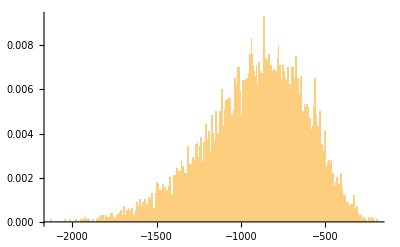

```mathematica
Histogram[simulationResults[[All,3]],500,"Probability"]
```

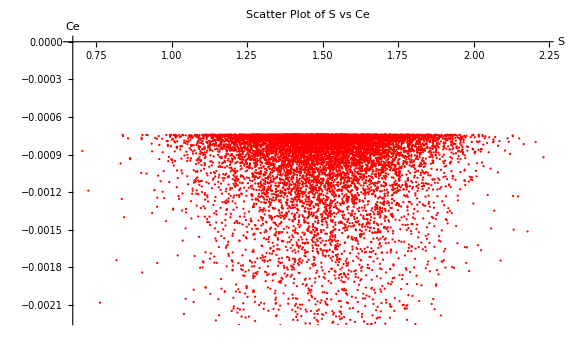

```mathematica
ListPlot[
simulationResults[[All,{1,3}]],
PlotStyle->Red,
AxesLabel->{"S","Ce"}, 
FrameLabel->{"S","Ce"},
LabelStyle->13,(*Increase the font size*)PlotLabel->Style["Scatter Plot of S vs Ce",20],(*Title of the plot*)TicksStyle->Directive[FontSize->15],(*Size of tick labels*)ImageSize->Large (*Makes the entire plot larger*)
]
```

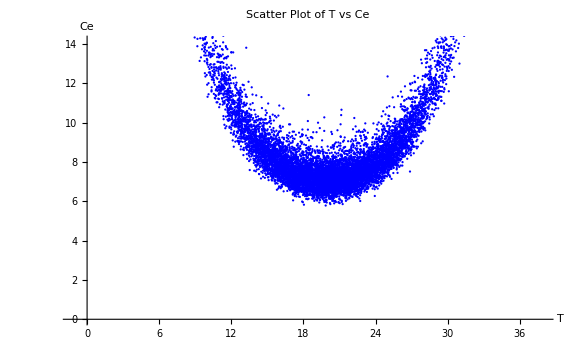

```mathematica
ListPlot[
simulationResults[[All,{2,3}]],
PlotStyle->Blue,
AxesLabel->{"T","Ce"}, 
FrameLabel->{"T","Ce"},
LabelStyle->13,(*Increase the font size*)PlotLabel->Style["Scatter Plot of T vs Ce",20],(*Title of the plot*)TicksStyle->Directive[FontSize->15],(*Size of tick labels*)ImageSize->Large (*Makes the entire plot larger*)
]
```

```mathematica
ListPlot3D[simulationResults,AxesLabel->{"S","T","Ce"},PlotStyle->Directive[PointSize[Medium],Blue],(*Customize point size and color*)LabelStyle->16,(*Make labels larger*)Boxed->True,ImageSize->Large,PlotRange->All
]
```

-Graphics3D-